#### Test interaction length module

```mathematica
(*FeTotalparamscoreT={{},{},{},{},{},{}};
Do[FeTotalparamscoreT[[i]]=Utilities`ReplaceParams[FeTotalparams[[i]],βcore,"β"],{i,Length[FeTotalparams]}];*)
```

```mathematica
(*EnergyLossTableAndInterFITTotalParamsEnhanced[{2.5 10^3,2.5 10^12} ("JpereV")/("c")^2/.SIConstRepl,{2 10^-4,2 10^-1} "c" /.SIConstRepl,<|"mχ"->8,"vχ"->4|>,FeTotalparamscoreT,,"FeELOutputDictSIEnhancedTest"]*)
```

```mathematica
(*EnergyLossMSIFitSumOscillatorsEnhanced[5 10^5 ("JpereV")/("c")^2/.SIConstRepl,2 10^-3"c" /.SIConstRepl,FeTotalparamscoreT,0]*)
```

```mathematica
(*EnergyLossMSIFitSumOscillatorsEnhanced[5 10^5 ("JpereV")/("c")^2/.SIConstRepl,2 10^-3"c" /.SIConstRepl,FeTotalparamscoreT,0]*)
```

```mathematica
(*EnergyLossMSIFitSumOscillatorsEnhanced[2.5 10^12 ("JpereV")/("c")^2/.SIConstRepl,2 10^-3"c" /.SIConstRepl,FeTotalparamscoreT,1]*)
```

### Compute Interaction Lengths - Pre Mistake

#### Load Parameters

```mathematica
FeTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/FeTotalparams"];
SiO2Totalparams= ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/SiO2Totalparams"];
MgOTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/MgOTotalparams"];
```

#### Run Iron

```mathematica
FeTotalparamscoreT={{},{},{},{},{},{}};
Do[FeTotalparamscoreT[[i]]=Utilities`ReplaceParams[FeTotalparams[[i]],βcore,"β"],{i,Length[FeTotalparams]}];
```

```mathematica
FeλeDictSI= EnergyLossTableAndInterFITTotalParamsEnhanced[{2.5 10^3,2.5 10^12} ("JpereV")/("c")^2/.SIConstRepl,{2 10^-4,2 10^-1} "c" /.SIConstRepl,<|"mχ"->8,"vχ"->4|>,FeTotalparamscoreT,True,"FeλeDictSI",0]
```

1 of 32

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1987.19}. NIntegrate obtained 0.000334844 and 3.4852×10^-6 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000334844 
Prefactor:	3.97147×10^12
dEdr:	1.32982×10^9

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {3559.6}. NIntegrate obtained 0.000269583 and 0.0000153292 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000269583 
Prefactor:	1.99412×10^12
dEdr:	5.3758×10^8

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {7257.97}. NIntegrate obtained 0.000177397 and 0.000012255 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000177397 
Prefactor:	1.90346×10^13
dEdr:	3.37667×10^9

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.0000490278 
Prefactor:	4.34962×10^13
dEdr:	2.13252×10^9

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

For mχ = 4.45×10^-33 , vχ = 60000
L:	3.02195×10^-6 
Prefactor:	5.18691×10^12
dEdr:	1.56746×10^7

For mχ = 4.45×10^-33 , vχ = 60000
L:	2.22176×10^-7 
Prefactor:	1.39275×10^11
dEdr:	30943.6

dEdr total: 7.3923×10^9

2 of 32

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.00304034 
Prefactor:	3.97147×10^10
dEdr:	1.20746×10^8

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.00275526 
Prefactor:	1.99412×10^10
dEdr:	5.49432×10^7

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.00149143 
Prefactor:	1.90346×10^11
dEdr:	2.83887×10^8

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.000490222 
Prefactor:	4.34962×10^11
dEdr:	2.13228×10^8

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.000030256 
Prefactor:	5.18691×10^10
dEdr:	1.56935×10^6

For mχ = 4.45×10^-33 , vχ = 600000
L:	2.22178×10^-6 
Prefactor:	1.39275×10^9
dEdr:	3094.39

dEdr total: 6.74376×10^8

3 of 32

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.0332471 
Prefactor:	3.97147×10^8
dEdr:	1.3204×10^7

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.02625 
Prefactor:	1.99412×10^8
dEdr:	5.23457×10^6

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.0157121 
Prefactor:	1.90346×10^9
dEdr:	2.99073×10^7

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.00491162 
Prefactor:	4.34962×10^9
dEdr:	2.13637×10^7

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.00030389 
Prefactor:	5.18691×10^8
dEdr:	157625.

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.0000222209 
Prefactor:	1.39275×10^7
dEdr:	309.482

dEdr total: 6.98675×10^7

4 of 32

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.678019 
Prefactor:	3.97147×10^6
dEdr:	2.69273×10^6

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.561138 
Prefactor:	1.99412×10^6
dEdr:	1.11898×10^6

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.311906 
Prefactor:	1.90346×10^7
dEdr:	5.93699×10^6

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.053064 
Prefactor:	4.34962×10^7
dEdr:	2.30808×10^6

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.00304627 
Prefactor:	5.18691×10^6
dEdr:	15800.7

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.000222098 
Prefactor:	139275.
dEdr:	30.9328

dEdr total: 1.20726×10^7

5 of 32

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.0015167 
Prefactor:	3.97147×10^12
dEdr:	6.02354×10^9

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.00122727 
Prefactor:	1.99412×10^12
dEdr:	2.44733×10^9

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.000748723 
Prefactor:	1.90346×10^13
dEdr:	1.42516×10^10

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.000224677 
Prefactor:	4.34962×10^13
dEdr:	9.77261×10^9

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.0000145461 
Prefactor:	5.18691×10^12
dEdr:	7.54494×10^7

For mχ = 8.5916×10^-32 , vχ = 60000
L:	1.09019×10^-6 
Prefactor:	1.39275×10^11
dEdr:	151837.

dEdr total: 3.25707×10^10

6 of 32

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.0151484 
Prefactor:	3.97147×10^10
dEdr:	6.01613×10^8

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.0122604 
Prefactor:	1.99412×10^10
dEdr:	2.44488×10^8

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.00748223 
Prefactor:	1.90346×10^11
dEdr:	1.42421×10^9

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.0022462 
Prefactor:	4.34962×10^11
dEdr:	9.77012×10^8

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.000145457 
Prefactor:	5.18691×10^10
dEdr:	7.54474×10^6

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.0000109019 
Prefactor:	1.39275×10^9
dEdr:	15183.6

dEdr total: 3.25488×10^9

7 of 32

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.166174 
Prefactor:	3.97147×10^8
dEdr:	6.59955×10^7

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.117227 
Prefactor:	1.99412×10^8
dEdr:	2.33765×10^7

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.0717915 
Prefactor:	1.90346×10^9
dEdr:	1.36652×10^8

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.0219851 
Prefactor:	4.34962×10^9
dEdr:	9.56268×10^7

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.00145078 
Prefactor:	5.18691×10^8
dEdr:	752505.

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.00010899 
Prefactor:	1.39275×10^7
dEdr:	1517.96

dEdr total: 3.22405×10^8

8 of 32

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	1.64738 
Prefactor:	3.97147×10^6
dEdr:	6.54253×10^6

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	1.35427 
Prefactor:	1.99412×10^6
dEdr:	2.70057×10^6

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.931225 
Prefactor:	1.90346×10^7
dEdr:	1.77255×10^7

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.355917 
Prefactor:	4.34962×10^7
dEdr:	1.5481×10^7

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.0173792 
Prefactor:	5.18691×10^6
dEdr:	90144.4

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.00106315 
Prefactor:	139275.
dEdr:	148.071

dEdr total: 4.25399×10^7

9 of 32

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.00207932 
Prefactor:	3.97147×10^12
dEdr:	8.25795×10^9

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.00141753 
Prefactor:	1.99412×10^12
dEdr:	2.82673×10^9

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.000922281 
Prefactor:	1.90346×10^13
dEdr:	1.75552×10^10

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.000300739 
Prefactor:	4.34962×10^13
dEdr:	1.3081×10^10

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.0000142552 
Prefactor:	5.18691×10^12
dEdr:	7.39407×10^7

For mχ = 1.65878×10^-30 , vχ = 60000
L:	7.22746×10^-7 
Prefactor:	1.39275×10^11
dEdr:	100661.

dEdr total: 4.17949×10^10

10 of 32

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.0251229 
Prefactor:	3.97147×10^10
dEdr:	9.97748×10^8

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.016317 
Prefactor:	1.99412×10^10
dEdr:	3.25379×10^8

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.0100138 
Prefactor:	1.90346×10^11
dEdr:	1.90608×10^9

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.0030771 
Prefactor:	4.34962×10^11
dEdr:	1.33842×10^9

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.000142747 
Prefactor:	5.18691×10^10
dEdr:	7.40414×10^6

For mχ = 1.65878×10^-30 , vχ = 600000
L:	7.22813×10^-6 
Prefactor:	1.39275×10^9
dEdr:	10067.

dEdr total: 4.57505×10^9

11 of 32

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.913892 
Prefactor:	3.97147×10^8
dEdr:	3.6295×10^8

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.746152 
Prefactor:	1.99412×10^8
dEdr:	1.48792×10^8

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.451739 
Prefactor:	1.90346×10^9
dEdr:	8.59866×10^8

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.0948244 
Prefactor:	4.34962×10^9
dEdr:	4.1245×10^8

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.00162755 
Prefactor:	5.18691×10^8
dEdr:	844198.

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.000072956 
Prefactor:	1.39275×10^7
dEdr:	1016.1

dEdr total: 1.7849×10^9

12 of 32

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	2.41705 
Prefactor:	3.97147×10^6
dEdr:	9.59923×10^6

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	1.98144 
Prefactor:	1.99412×10^6
dEdr:	3.95124×10^6

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	1.4093 
Prefactor:	1.90346×10^7
dEdr:	2.68255×10^7

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.604057 
Prefactor:	4.34962×10^7
dEdr:	2.62742×10^7

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.0695256 
Prefactor:	5.18691×10^6
dEdr:	360623.

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.0015161 
Prefactor:	139275.
dEdr:	211.155

dEdr total: 6.70109×10^7

13 of 32

For mχ = 3.2026×10^-29 , vχ = 60000
L:	4.45384×10^-7 
Prefactor:	3.97147×10^12
dEdr:	1.76883×10^6

For mχ = 3.2026×10^-29 , vχ = 60000
L:	1.09385×10^-6 
Prefactor:	1.99412×10^12
dEdr:	2.18127×10^6

For mχ = 3.2026×10^-29 , vχ = 60000
L:	1.24836×10^-6 
Prefactor:	1.90346×10^13
dEdr:	2.37621×10^7

For mχ = 3.2026×10^-29 , vχ = 60000
L:	6.51249×10^-7 
Prefactor:	4.34962×10^13
dEdr:	2.83268×10^7

For mχ = 3.2026×10^-29 , vχ = 60000
L:	3.46417×10^-8 
Prefactor:	5.18691×10^12
dEdr:	179684.

For mχ = 3.2026×10^-29 , vχ = 60000
L:	1.74597×10^-9 
Prefactor:	1.39275×10^11
dEdr:	243.171

dEdr total: 5.62189×10^7

14 of 32

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.00613187 
Prefactor:	3.97147×10^10
dEdr:	2.43525×10^8

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.00251533 
Prefactor:	1.99412×10^10
dEdr:	5.01587×10^7

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.00108841 
Prefactor:	1.90346×10^11
dEdr:	2.07174×10^8

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.000128024 
Prefactor:	4.34962×10^11
dEdr:	5.56854×10^7

For mχ = 3.2026×10^-29 , vχ = 600000
L:	6.13817×10^-7 
Prefactor:	5.18691×10^10
dEdr:	31838.2

For mχ = 3.2026×10^-29 , vχ = 600000
L:	1.82633×10^-8 
Prefactor:	1.39275×10^9
dEdr:	25.4363

dEdr total: 5.56575×10^8

15 of 32

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.924532 
Prefactor:	3.97147×10^8
dEdr:	3.67175×10^8

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.755579 
Prefactor:	1.99412×10^8
dEdr:	1.50671×10^8

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.461147 
Prefactor:	1.90346×10^9
dEdr:	8.77774×10^8

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.0943591 
Prefactor:	4.34962×10^9
dEdr:	4.10426×10^8

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.000352954 
Prefactor:	5.18691×10^8
dEdr:	183074.

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	1.1831×10^-6 
Prefactor:	1.39275×10^7
dEdr:	16.4776

dEdr total: 1.80623×10^9

16 of 32

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	2.42274 
Prefactor:	3.97147×10^6
dEdr:	9.62183×10^6

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	1.98606 
Prefactor:	1.99412×10^6
dEdr:	3.96044×10^6

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	1.41285 
Prefactor:	1.90346×10^7
dEdr:	2.6893×10^7

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.605987 
Prefactor:	4.34962×10^7
dEdr:	2.63581×10^7

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.0701992 
Prefactor:	5.18691×10^6
dEdr:	364117.

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.00115113 
Prefactor:	139275.
dEdr:	160.324

dEdr total: 6.71976×10^7

17 of 32

For mχ = 6.18325×10^-28 , vχ = 60000
L:	4.75855×10^-6 
Prefactor:	3.97147×10^12
dEdr:	1.88985×10^7

For mχ = 6.18325×10^-28 , vχ = 60000
L:	1.9183×10^-6 
Prefactor:	1.99412×10^12
dEdr:	3.82532×10^6

For mχ = 6.18325×10^-28 , vχ = 60000
L:	8.49412×10^-7 
Prefactor:	1.90346×10^13
dEdr:	1.61682×10^7

For mχ = 6.18325×10^-28 , vχ = 60000
L:	1.03781×10^-7 
Prefactor:	4.34962×10^13
dEdr:	4.51407×10^6

For mχ = 6.18325×10^-28 , vχ = 60000
L:	3.48524×10^-10 
Prefactor:	5.18691×10^12
dEdr:	1807.77

For mχ = 6.18325×10^-28 , vχ = 60000
L:	5.43499×10^-12 
Prefactor:	1.39275×10^11
dEdr:	0.756959

dEdr total: 4.34079×10^7

18 of 32

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.00646301 
Prefactor:	3.97147×10^10
dEdr:	2.56677×10^8

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.00267166 
Prefactor:	1.99412×10^10
dEdr:	5.3276×10^7

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.00116499 
Prefactor:	1.90346×10^11
dEdr:	2.2175×10^8

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.000138293 
Prefactor:	4.34962×10^11
dEdr:	6.01523×10^7

For mχ = 6.18325×10^-28 , vχ = 600000
L:	3.60909×10^-7 
Prefactor:	5.18691×10^10
dEdr:	18720.1

For mχ = 6.18325×10^-28 , vχ = 600000
L:	1.12799×10^-9 
Prefactor:	1.39275×10^9
dEdr:	1.57101

dEdr total: 5.91874×10^8

19 of 32

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.927594 
Prefactor:	3.97147×10^8
dEdr:	3.68391×10^8

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.758091 
Prefactor:	1.99412×10^8
dEdr:	1.51172×10^8

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.463177 
Prefactor:	1.90346×10^9
dEdr:	8.81637×10^8

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.095328 
Prefactor:	4.34962×10^9
dEdr:	4.14641×10^8

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.00036874 
Prefactor:	5.18691×10^8
dEdr:	191262.

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	1.18784×10^-6 
Prefactor:	1.39275×10^7
dEdr:	16.5437

dEdr total: 1.81603×10^9

20 of 32

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	2.42554 
Prefactor:	3.97147×10^6
dEdr:	9.63296×10^6

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	1.98834 
Prefactor:	1.99412×10^6
dEdr:	3.96498×10^6

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	1.41459 
Prefactor:	1.90346×10^7
dEdr:	2.6926×10^7

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.606886 
Prefactor:	4.34962×10^7
dEdr:	2.63972×10^7

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.0703919 
Prefactor:	5.18691×10^6
dEdr:	365117.

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.0011718 
Prefactor:	139275.
dEdr:	163.203

dEdr total: 6.72865×10^7

21 of 32

For mχ = 1.1938×10^-26 , vχ = 60000
L:	5.26428×10^-6 
Prefactor:	3.97147×10^12
dEdr:	2.09069×10^7

For mχ = 1.1938×10^-26 , vχ = 60000
L:	2.12545×10^-6 
Prefactor:	1.99412×10^12
dEdr:	4.2384×10^6

For mχ = 1.1938×10^-26 , vχ = 60000
L:	9.43961×10^-7 
Prefactor:	1.90346×10^13
dEdr:	1.79679×10^7

For mχ = 1.1938×10^-26 , vχ = 60000
L:	1.16595×10^-7 
Prefactor:	4.34962×10^13
dEdr:	5.07144×10^6

For mχ = 1.1938×10^-26 , vχ = 60000
L:	3.40299×10^-10 
Prefactor:	5.18691×10^12
dEdr:	1765.1

For mχ = 1.1938×10^-26 , vχ = 60000
L:	1.11378×10^-12 
Prefactor:	1.39275×10^11
dEdr:	0.155121

dEdr total: 4.81864×10^7

22 of 32

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00648361 
Prefactor:	3.97147×10^10
dEdr:	2.57495×10^8

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00268194 
Prefactor:	1.99412×10^10
dEdr:	5.3481×10^7

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.0011704 
Prefactor:	1.90346×10^11
dEdr:	2.2278×10^8

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.000139343 
Prefactor:	4.34962×10^11
dEdr:	6.06087×10^7

For mχ = 1.1938×10^-26 , vχ = 600000
L:	3.70676×10^-7 
Prefactor:	5.18691×10^10
dEdr:	19226.6

For mχ = 1.1938×10^-26 , vχ = 600000
L:	1.19142×10^-9 
Prefactor:	1.39275×10^9
dEdr:	1.65935

dEdr total: 5.94383×10^8

23 of 32

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.927759 
Prefactor:	3.97147×10^8
dEdr:	3.68457×10^8

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.758226 
Prefactor:	1.99412×10^8
dEdr:	1.51199×10^8

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.463286 
Prefactor:	1.90346×10^9
dEdr:	8.81844×10^8

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.0953808 
Prefactor:	4.34962×10^9
dEdr:	4.1487×10^8

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.000369795 
Prefactor:	5.18691×10^8
dEdr:	191810.

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	1.20028×10^-6 
Prefactor:	1.39275×10^7
dEdr:	16.7169

dEdr total: 1.81656×10^9

24 of 32

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	2.42569 
Prefactor:	3.97147×10^6
dEdr:	9.63354×10^6

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	1.98846 
Prefactor:	1.99412×10^6
dEdr:	3.96523×10^6

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	1.41468 
Prefactor:	1.90346×10^7
dEdr:	2.69278×10^7

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.606935 
Prefactor:	4.34962×10^7
dEdr:	2.63993×10^7

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.0704023 
Prefactor:	5.18691×10^6
dEdr:	365171.

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.00117298 
Prefactor:	139275.
dEdr:	163.367

dEdr total: 6.72913×10^7

25 of 32

For mχ = 2.30487×10^-25 , vχ = 60000
L:	5.29129×10^-6 
Prefactor:	3.97147×10^12
dEdr:	2.10142×10^7

For mχ = 2.30487×10^-25 , vχ = 60000
L:	2.13666×10^-6 
Prefactor:	1.99412×10^12
dEdr:	4.26076×10^6

For mχ = 2.30487×10^-25 , vχ = 60000
L:	9.49205×10^-7 
Prefactor:	1.90346×10^13
dEdr:	1.80677×10^7

For mχ = 2.30487×10^-25 , vχ = 60000
L:	1.17394×10^-7 
Prefactor:	4.34962×10^13
dEdr:	5.10618×10^6

For mχ = 2.30487×10^-25 , vχ = 60000
L:	3.46276×10^-10 
Prefactor:	5.18691×10^12
dEdr:	1796.1

For mχ = 2.30487×10^-25 , vχ = 60000
L:	1.16538×10^-12 
Prefactor:	1.39275×10^11
dEdr:	0.162309

dEdr total: 4.84506×10^7

26 of 32

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00648468 
Prefactor:	3.97147×10^10
dEdr:	2.57537×10^8

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00268248 
Prefactor:	1.99412×10^10
dEdr:	5.34918×10^7

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00117068 
Prefactor:	1.90346×10^11
dEdr:	2.22834×10^8

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.000139398 
Prefactor:	4.34962×10^11
dEdr:	6.0633×10^7

For mχ = 2.30487×10^-25 , vχ = 600000
L:	3.7125×10^-7 
Prefactor:	5.18691×10^10
dEdr:	19256.4

For mχ = 2.30487×10^-25 , vχ = 600000
L:	1.19806×10^-9 
Prefactor:	1.39275×10^9
dEdr:	1.6686

dEdr total: 5.94515×10^8

27 of 32

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.927768 
Prefactor:	3.97147×10^8
dEdr:	3.6846×10^8

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.758233 
Prefactor:	1.99412×10^8
dEdr:	1.51201×10^8

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.463292 
Prefactor:	1.90346×10^9
dEdr:	8.81855×10^8

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.0953835 
Prefactor:	4.34962×10^9
dEdr:	4.14882×10^8

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.000369851 
Prefactor:	5.18691×10^8
dEdr:	191838.

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	1.20096×10^-6 
Prefactor:	1.39275×10^7
dEdr:	16.7264

dEdr total: 1.81659×10^9

28 of 32

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	2.4257 
Prefactor:	3.97147×10^6
dEdr:	9.63359×10^6

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	1.98847 
Prefactor:	1.99412×10^6
dEdr:	3.96525×10^6

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	1.41468 
Prefactor:	1.90346×10^7
dEdr:	2.69279×10^7

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.606937 
Prefactor:	4.34962×10^7
dEdr:	2.63994×10^7

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.0704029 
Prefactor:	5.18691×10^6
dEdr:	365174.

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.00117304 
Prefactor:	139275.
dEdr:	163.375

dEdr total: 6.72915×10^7

29 of 32

For mχ = 4.45×10^-24 , vχ = 60000
L:	5.29269×10^-6 
Prefactor:	3.97147×10^12
dEdr:	2.10198×10^7

For mχ = 4.45×10^-24 , vχ = 60000
L:	2.13725×10^-6 
Prefactor:	1.99412×10^12
dEdr:	4.26192×10^6

For mχ = 4.45×10^-24 , vχ = 60000
L:	9.49478×10^-7 
Prefactor:	1.90346×10^13
dEdr:	1.80729×10^7

For mχ = 4.45×10^-24 , vχ = 60000
L:	1.17436×10^-7 
Prefactor:	4.34962×10^13
dEdr:	5.108×10^6

For mχ = 4.45×10^-24 , vχ = 60000
L:	3.46604×10^-10 
Prefactor:	5.18691×10^12
dEdr:	1797.8

For mχ = 4.45×10^-24 , vχ = 60000
L:	1.16896×10^-12 
Prefactor:	1.39275×10^11
dEdr:	0.162808

dEdr total: 4.84644×10^7

30 of 32

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.00648474 
Prefactor:	3.97147×10^10
dEdr:	2.5754×10^8

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.0026825 
Prefactor:	1.99412×10^10
dEdr:	5.34923×10^7

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.00117069 
Prefactor:	1.90346×10^11
dEdr:	2.22836×10^8

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.000139401 
Prefactor:	4.34962×10^11
dEdr:	6.06342×10^7

For mχ = 4.45×10^-24 , vχ = 600000
L:	3.71279×10^-7 
Prefactor:	5.18691×10^10
dEdr:	19257.9

For mχ = 4.45×10^-24 , vχ = 600000
L:	1.19842×10^-9 
Prefactor:	1.39275×10^9
dEdr:	1.6691

dEdr total: 5.94522×10^8

31 of 32

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.927768 
Prefactor:	3.97147×10^8
dEdr:	3.68461×10^8

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.758234 
Prefactor:	1.99412×10^8
dEdr:	1.51201×10^8

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.463292 
Prefactor:	1.90346×10^9
dEdr:	8.81856×10^8

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.0953837 
Prefactor:	4.34962×10^9
dEdr:	4.14883×10^8

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.000369854 
Prefactor:	5.18691×10^8
dEdr:	191840.

For mχ = 4.45×10^-24 , vχ = 6000000
L:	1.20099×10^-6 
Prefactor:	1.39275×10^7
dEdr:	16.7269

dEdr total: 1.81659×10^9

32 of 32

For mχ = 4.45×10^-24 , vχ = 60000000
L:	2.4257 
Prefactor:	3.97147×10^6
dEdr:	9.63359×10^6

For mχ = 4.45×10^-24 , vχ = 60000000
L:	1.98847 
Prefactor:	1.99412×10^6
dEdr:	3.96525×10^6

For mχ = 4.45×10^-24 , vχ = 60000000
L:	1.41469 
Prefactor:	1.90346×10^7
dEdr:	2.69279×10^7

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.606937 
Prefactor:	4.34962×10^7
dEdr:	2.63995×10^7

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.0704029 
Prefactor:	5.18691×10^6
dEdr:	365174.

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.00117304 
Prefactor:	139275.
dEdr:	163.376

dEdr total: 6.72915×10^7

<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{7.3923×10^9,6.74376×10^8,6.98675×10^7,1.20726×10^7},{3.25707×10^10,3.25488×10^9,3.22405×10^8,4.25399×10^7},{4.17949×10^10,4.57505×10^9,1.7849×10^9,6.70109×10^7},{5.62189×10^7,5.56575×10^8,1.80623×10^9,6.71976×10^7},{4.34079×10^7,5.91874×10^8,1.81603×10^9,6.72865×10^7},{4.81864×10^7,5.94383×10^8,1.81656×10^9,6.72913×10^7},{4.84506×10^7,5.94515×10^8,1.81659×10^9,6.72915×10^7},{4.84644×10^7,5.94522×10^8,1.81659×10^9,6.72915×10^7}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→1.038×10^29,qF→1.45392×10^10,vF→1.68373×10^6,μ→1.29132×10^-18,ωp→1.81874×10^16,α→1/137,χ→0.643411,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→322.436,nI→1.2975×10^28,Z→8,M→9.27329×10^-26,EF→1.29132×10^-18,ωi→1.81874×10^16,νi→1.75116×10^16,Ai→0.209474,ωedgei→6.04519×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→1.91532×10^29,qF→1.78329×10^10,vF→2.06517×10^6,μ→1.94267×10^-18,ωp→2.47055×10^16,α→1/137,χ→0.580962,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→485.073,nI→2.39415×10^28,Z→8,M→9.27329×10^-26,EF→1.94267×10^-18,ωi→2.47055×10^16,νi→8.99966×10^15,Ai→0.0699144,ωedgei→6.5887×10^12},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→4.34359×10^29,qF→2.34292×10^10,vF→2.71326×10^6,μ→3.35328×10^-18,ωp→3.72046×10^16,α→1/137,χ→0.506851,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→837.295,nI→5.42949×10^28,Z→8,M→9.27329×10^-26,EF→3.35328×10^-18,ωi→3.72046×10^16,νi→2.01886×10^16,Ai→0.386622,ωedgei→3.02977×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→3.17873×10^30,qF→4.54874×10^10,vF→5.26776×10^6,μ→1.26398×10^-17,ωp→1.00647×10^17,α→1/137,χ→0.363758,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→3156.08,nI→3.97341×10^29,Z→8,M→9.27329×10^-26,EF→1.26398×10^-17,ωi→1.00647×10^17,νi→9.30837×10^16,Ai→0.234383,ωedgei→1.51848×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→4.14995×10^32,qF→2.30757×10^11,vF→2.67232×10^7,μ→3.25286×10^-16,ωp→1.14999×10^18,α→1/137,χ→0.161503,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→81222.,nI→5.18743×10^31,Z→8,M→9.27329×10^-26,EF→3.25286×10^-16,ωi→1.14999×10^18,νi→7.408×10^17,Ai→0.00108607,ωedgei→1.09042×10^18},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→4.0004×10^34,qF→1.05805×10^12,vF→1.2253×10^8,μ→6.83868×10^-15,ωp→1.12908×10^19,α→1/137,χ→0.0754231,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→1.70758×10^6,nI→5.00049×10^33,Z→8,M→9.27329×10^-26,EF→6.83868×10^-15,ωi→1.12908×10^19,νi→5.21962×10^18,Ai→1.38712×10^-6,ωedgei→1.09893×10^19}},fname→FeλeDictSI,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{6928.07,2814.89,1938.6,1345.6},{34.028,37.0543,57.0632,231.725},{27.4128,31.9165,83.9904,397.678},{36.9383,72.7746,87.4015,342.15},{86.5879,88.1746,79.0239,417.38},{124.484,111.202,104.756,424.336},{130.656,110.464,102.221,645.321},{124.361,109.449,99.4333,423.281}},totalTime→17648.4|>

#### Plot Iron

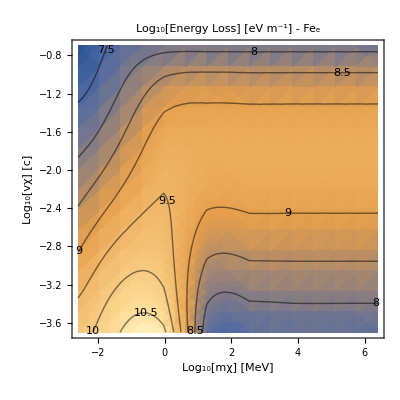

```mathematica
EnergyLoss`PlotEL[FeλeDictSI,"Fe_e"]
```

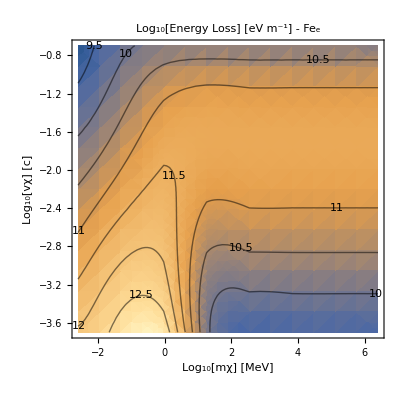

#### Run SiO2

```mathematica
SiO2λeDictSI= EnergyLossTableAndInterFITTotalParamsEnhanced[{2.5 10^3,2.5 10^12} ("JpereV")/("c")^2/.SIConstRepl,{2 10^-4,2 10^-1} "c" /.SIConstRepl,<|"mχ"->8,"vχ"->4|>,SiO2Totalparams,True,"SiO2λeDictSI",0]
```

1 of 32

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000175393 
Prefactor:	2.60571×10^13
dEdr:	4.57024×10^9

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {3559.6}. NIntegrate obtained 0.00006384 and 2.53169×10^-6 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.00006384 
Prefactor:	1.19243×10^13
dEdr:	7.61245×10^8

dEdr total: 5.33148×10^9

2 of 32

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {3559.6}. NIntegrate obtained 0.001771 and 0.0000717928 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.001771 
Prefactor:	2.60571×10^11
dEdr:	4.61471×10^8

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {3559.6}. NIntegrate obtained 0.000631085 and 0.0000248038 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.000631085 
Prefactor:	1.19243×10^11
dEdr:	7.52522×10^7

dEdr total: 5.36723×10^8

3 of 32

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.0172835 
Prefactor:	2.60571×10^9
dEdr:	4.50358×10^7

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.00660997 
Prefactor:	1.19243×10^9
dEdr:	7.8819×10^6

dEdr total: 5.29177×10^7

4 of 32

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.327776 
Prefactor:	2.60571×10^7
dEdr:	8.5409×10^6

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.079298 
Prefactor:	1.19243×10^7
dEdr:	945570.

dEdr total: 9.48647×10^6

5 of 32

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.000797277 
Prefactor:	2.60571×10^13
dEdr:	2.07747×10^10

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.000305998 
Prefactor:	1.19243×10^13
dEdr:	3.6488×10^9

dEdr total: 2.44235×10^10

6 of 32

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.00796714 
Prefactor:	2.60571×10^11
dEdr:	2.076×10^9

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.00305899 
Prefactor:	1.19243×10^11
dEdr:	3.64762×10^8

dEdr total: 2.44077×10^9

7 of 32

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.076435 
Prefactor:	2.60571×10^9
dEdr:	1.99167×10^8

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.0297862 
Prefactor:	1.19243×10^9
dEdr:	3.55178×10^7

dEdr total: 2.34685×10^8

8 of 32

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.961386 
Prefactor:	2.60571×10^7
dEdr:	2.50509×10^7

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.454893 
Prefactor:	1.19243×10^7
dEdr:	5.42427×10^6

dEdr total: 3.04752×10^7

9 of 32

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.000992502 
Prefactor:	2.60571×10^13
dEdr:	2.58617×10^10

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.000394726 
Prefactor:	1.19243×10^13
dEdr:	4.70682×10^9

dEdr total: 3.05685×10^10

10 of 32

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.0107805 
Prefactor:	2.60571×10^11
dEdr:	2.80908×10^9

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.00406926 
Prefactor:	1.19243×10^11
dEdr:	4.85229×10^8

dEdr total: 3.29431×10^9

11 of 32

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.468181 
Prefactor:	2.60571×10^9
dEdr:	1.21994×10^9

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.144233 
Prefactor:	1.19243×10^9
dEdr:	1.71988×10^8

dEdr total: 1.39193×10^9

12 of 32

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	1.45001 
Prefactor:	2.60571×10^7
dEdr:	3.7783×10^7

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.74311 
Prefactor:	1.19243×10^7
dEdr:	8.86104×10^6

dEdr total: 4.6644×10^7

13 of 32

For mχ = 3.2026×10^-29 , vχ = 60000
L:	2.97971×10^-6 
Prefactor:	2.60571×10^13
dEdr:	7.76425×10^7

For mχ = 3.2026×10^-29 , vχ = 60000
L:	1.07087×10^-6 
Prefactor:	1.19243×10^13
dEdr:	1.27693×10^7

dEdr total: 9.04117×10^7

14 of 32

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.00125824 
Prefactor:	2.60571×10^11
dEdr:	3.2786×10^8

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.000214061 
Prefactor:	1.19243×10^11
dEdr:	2.55252×10^7

dEdr total: 3.53385×10^8

15 of 32

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.477385 
Prefactor:	2.60571×10^9
dEdr:	1.24393×10^9

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.147334 
Prefactor:	1.19243×10^9
dEdr:	1.75685×10^8

dEdr total: 1.41961×10^9

16 of 32

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	1.45363 
Prefactor:	2.60571×10^7
dEdr:	3.78773×10^7

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.745309 
Prefactor:	1.19243×10^7
dEdr:	8.88726×10^6

dEdr total: 4.67645×10^7

17 of 32

For mχ = 6.18325×10^-28 , vχ = 60000
L:	1.27123×10^-6 
Prefactor:	2.60571×10^13
dEdr:	3.31244×10^7

For mχ = 6.18325×10^-28 , vχ = 60000
L:	2.16379×10^-7 
Prefactor:	1.19243×10^13
dEdr:	2.58016×10^6

dEdr total: 3.57046×10^7

18 of 32

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.0013328 
Prefactor:	2.60571×10^11
dEdr:	3.4729×10^8

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.000229303 
Prefactor:	1.19243×10^11
dEdr:	2.73427×10^7

dEdr total: 3.74632×10^8

19 of 32

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.479441 
Prefactor:	2.60571×10^9
dEdr:	1.24928×10^9

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.148592 
Prefactor:	1.19243×10^9
dEdr:	1.77185×10^8

dEdr total: 1.42647×10^9

20 of 32

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	1.4554 
Prefactor:	2.60571×10^7
dEdr:	3.79235×10^7

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.746355 
Prefactor:	1.19243×10^7
dEdr:	8.89973×10^6

dEdr total: 4.68233×10^7

21 of 32

For mχ = 1.1938×10^-26 , vχ = 60000
L:	1.32068×10^-6 
Prefactor:	2.60571×10^13
dEdr:	3.44131×10^7

For mχ = 1.1938×10^-26 , vχ = 60000
L:	2.28052×10^-7 
Prefactor:	1.19243×10^13
dEdr:	2.71936×10^6

dEdr total: 3.71324×10^7

22 of 32

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00133819 
Prefactor:	2.60571×10^11
dEdr:	3.48694×10^8

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.000230744 
Prefactor:	1.19243×10^11
dEdr:	2.75146×10^7

dEdr total: 3.76208×10^8

23 of 32

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.479552 
Prefactor:	2.60571×10^9
dEdr:	1.24957×10^9

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.14866 
Prefactor:	1.19243×10^9
dEdr:	1.77267×10^8

dEdr total: 1.42684×10^9

24 of 32

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	1.4555 
Prefactor:	2.60571×10^7
dEdr:	3.7926×10^7

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.746411 
Prefactor:	1.19243×10^7
dEdr:	8.90041×10^6

dEdr total: 4.68265×10^7

25 of 32

For mχ = 2.30487×10^-25 , vχ = 60000
L:	1.32366×10^-6 
Prefactor:	2.60571×10^13
dEdr:	3.44907×10^7

For mχ = 2.30487×10^-25 , vχ = 60000
L:	2.28838×10^-7 
Prefactor:	1.19243×10^13
dEdr:	2.72872×10^6

dEdr total: 3.72195×10^7

26 of 32

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00133847 
Prefactor:	2.60571×10^11
dEdr:	3.48768×10^8

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.000230821 
Prefactor:	1.19243×10^11
dEdr:	2.75237×10^7

dEdr total: 3.76291×10^8

27 of 32

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.479557 
Prefactor:	2.60571×10^9
dEdr:	1.24959×10^9

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.148664 
Prefactor:	1.19243×10^9
dEdr:	1.77271×10^8

dEdr total: 1.42686×10^9

28 of 32

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	1.4555 
Prefactor:	2.60571×10^7
dEdr:	3.79262×10^7

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.746414 
Prefactor:	1.19243×10^7
dEdr:	8.90044×10^6

dEdr total: 4.68266×10^7

29 of 32

For mχ = 4.45×10^-24 , vχ = 60000
L:	1.32382×10^-6 
Prefactor:	2.60571×10^13
dEdr:	3.44948×10^7

For mχ = 4.45×10^-24 , vχ = 60000
L:	2.28879×10^-7 
Prefactor:	1.19243×10^13
dEdr:	2.72921×10^6

dEdr total: 3.7224×10^7

30 of 32

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.00133849 
Prefactor:	2.60571×10^11
dEdr:	3.48771×10^8

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.000230825 
Prefactor:	1.19243×10^11
dEdr:	2.75242×10^7

dEdr total: 3.76296×10^8

31 of 32

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.479558 
Prefactor:	2.60571×10^9
dEdr:	1.24959×10^9

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.148664 
Prefactor:	1.19243×10^9
dEdr:	1.77271×10^8

dEdr total: 1.42686×10^9

32 of 32

For mχ = 4.45×10^-24 , vχ = 60000000
L:	1.4555 
Prefactor:	2.60571×10^7
dEdr:	3.79262×10^7

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.746414 
Prefactor:	1.19243×10^7
dEdr:	8.90044×10^6

dEdr total: 4.68266×10^7

<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{5.33148×10^9,5.36723×10^8,5.29177×10^7,9.48647×10^6},{2.44235×10^10,2.44077×10^9,2.34685×10^8,3.04752×10^7},{3.05685×10^10,3.29431×10^9,1.39193×10^9,4.6644×10^7},{9.04117×10^7,3.53385×10^8,1.41961×10^9,4.67645×10^7},{3.57046×10^7,3.74632×10^8,1.42647×10^9,4.68233×10^7},{3.71324×10^7,3.76208×10^8,1.42684×10^9,4.68265×10^7},{3.72195×10^7,3.76291×10^8,1.42686×10^9,4.68266×10^7},{3.7224×10^7,3.76296×10^8,1.42686×10^9,4.68266×10^7}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.07027×10^29,qF→2.2927×10^10,vF→2.65511×10^6,μ→3.21109×10^-18,ωp→3.60151×10^16,α→1/137,χ→0.512371,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→801.791,nI→5.08784×10^28,Z→8,M→9.27329×10^-26,EF→3.21109×10^-18,ωi→3.60151×10^16,νi→2.11534×10^16,Ai→0.552697,ωedgei→0},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→2.0121×10^30,qF→3.90562×10^10,vF→4.52297×10^6,μ→9.3183×10^-18,ωp→8.0075×10^16,α→1/137,χ→0.392567,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→2326.72,nI→2.51512×10^29,Z→8,M→9.27329×10^-26,EF→9.3183×10^-18,ωi→8.0075×10^16,νi→6.06034×10^16,Ai→0.0871584,ωedgei→0}},fname→SiO2λeDictSI,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{334.657,464.641,412.185,469.645},{11.074,10.4926,14.896,84.078},{10.9539,11.8907,26.009,224.262},{13.3242,17.6468,18.9882,142.627},{31.1561,12.2777,18.1718,109.137},{22.7154,10.9063,17.8597,108.507},{42.9443,17.8756,26.8429,123.07},{22.7933,9.7876,17.2766,113.11}},totalTime→2971.8|>

#### Plot SiO2

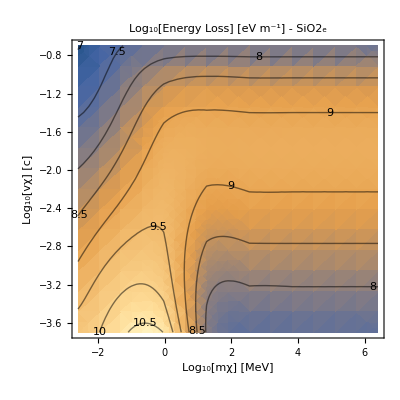

```mathematica
EnergyLoss`PlotEL[SiO2λeDictSI,"SiO2_e"]
```

#### Run MgO

```mathematica
(*MgOλeDictSI= EnergyLossTableAndInterFITTotalParamsEnhanced[{2.5 10^3,2.5 10^12} ("JpereV")/("c")^2/.SIConstRepl,{2 10^-4,2 10^-1} "c" /.SIConstRepl,<|"mχ"->8,"vχ"->4|>,MgOTotalparams,True,"MgOλeDictSI"]*)
```

1 of 32

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1987.19}. NIntegrate obtained 0.000337559 and 4.38616×10^-6 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000337559 
Prefactor:	3.99192×10^13
dEdr:	1.34751×10^10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1983.01}. NIntegrate obtained 0.000208341 and 1.08951×10^-6 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000208341 
Prefactor:	5.73915×10^14
dEdr:	1.1957×10^11

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {3559.6}. NIntegrate obtained 0.000182741 and 4.01308×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000182741 
Prefactor:	4.00973×10^14
dEdr:	7.32741×10^10

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.0000668434 
Prefactor:	1.00279×10^16
dEdr:	6.703×10^11

dEdr total: 8.76619×10^11

2 of 32

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.00337213 
Prefactor:	3.99192×10^11
dEdr:	1.34613×10^9

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.00214005 
Prefactor:	5.73915×10^12
dEdr:	1.22821×10^10

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.00183626 
Prefactor:	4.00973×10^12
dEdr:	7.36293×10^9

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.000596438 
Prefactor:	1.00279×10^14
dEdr:	5.98103×10^10

dEdr total: 8.08015×10^10

3 of 32

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.0339014 
Prefactor:	3.99192×10^9
dEdr:	1.35332×10^8

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.0208949 
Prefactor:	5.73915×10^10
dEdr:	1.19919×10^9

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.018411 
Prefactor:	4.00973×10^10
dEdr:	7.38233×10^8

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.006315 
Prefactor:	1.00279×10^12
dEdr:	6.33263×10^9

dEdr total: 8.40538×10^9

4 of 32

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.688955 
Prefactor:	3.99192×10^7
dEdr:	2.75026×10^7

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.420291 
Prefactor:	5.73915×10^8
dEdr:	2.41211×10^8

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.370221 
Prefactor:	4.00973×10^8
dEdr:	1.48449×10^8

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.0834964 
Prefactor:	1.00279×10^10
dEdr:	8.37294×10^8

dEdr total: 1.25446×10^9

5 of 32

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.00154969 
Prefactor:	3.99192×10^13
dEdr:	6.18623×10^10

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.000950025 
Prefactor:	5.73915×10^14
dEdr:	5.45234×10^11

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.000848748 
Prefactor:	4.00973×10^14
dEdr:	3.40325×10^11

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.000302277 
Prefactor:	1.00279×10^16
dEdr:	3.03121×10^12

dEdr total: 3.97863×10^12

6 of 32

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.0154786 
Prefactor:	3.99192×10^11
dEdr:	6.17895×10^9

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.00949283 
Prefactor:	5.73915×10^12
dEdr:	5.44808×10^10

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.00848144 
Prefactor:	4.00973×10^12
dEdr:	3.40083×10^10

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.00302172 
Prefactor:	1.00279×10^14
dEdr:	3.03015×10^11

dEdr total: 3.97683×10^11

7 of 32

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.14523 
Prefactor:	3.99192×10^9
dEdr:	5.79748×10^8

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.0894217 
Prefactor:	5.73915×10^10
dEdr:	5.13205×10^9

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.080161 
Prefactor:	4.00973×10^10
dEdr:	3.21424×10^9

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.029554 
Prefactor:	1.00279×10^12
dEdr:	2.96365×10^10

dEdr total: 3.85625×10^10

8 of 32

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	1.55492 
Prefactor:	3.99192×10^7
dEdr:	6.20714×10^7

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	1.07773 
Prefactor:	5.73915×10^8
dEdr:	6.18526×10^8

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.989519 
Prefactor:	4.00973×10^8
dEdr:	3.9677×10^8

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.455491 
Prefactor:	1.00279×10^10
dEdr:	4.56763×10^9

dEdr total: 5.64499×10^9

9 of 32

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.00167282 
Prefactor:	3.99192×10^13
dEdr:	6.67777×10^10

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.00102198 
Prefactor:	5.73915×10^14
dEdr:	5.86528×10^11

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.000910984 
Prefactor:	4.00973×10^14
dEdr:	3.6528×10^11

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.000477238 
Prefactor:	1.00279×10^16
dEdr:	4.7857×10^12

dEdr total: 5.80429×10^12

10 of 32

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.0195732 
Prefactor:	3.99192×10^11
dEdr:	7.81349×10^9

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.0112008 
Prefactor:	5.73915×10^12
dEdr:	6.4283×10^10

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.00987762 
Prefactor:	4.00973×10^12
dEdr:	3.96066×10^10

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.00491014 
Prefactor:	1.00279×10^14
dEdr:	4.92384×10^11

dEdr total: 6.04087×10^11

11 of 32

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.889273 
Prefactor:	3.99192×10^9
dEdr:	3.54991×10^9

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.564989 
Prefactor:	5.73915×10^10
dEdr:	3.24256×10^10

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.505175 
Prefactor:	4.00973×10^10
dEdr:	2.02562×10^10

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.148432 
Prefactor:	1.00279×10^12
dEdr:	1.48846×10^11

dEdr total: 2.05078×10^11

12 of 32

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	2.23428 
Prefactor:	3.99192×10^7
dEdr:	8.91907×10^7

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	1.58689 
Prefactor:	5.73915×10^8
dEdr:	9.10741×10^8

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	1.46595 
Prefactor:	4.00973×10^8
dEdr:	5.87806×10^8

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.766219 
Prefactor:	1.00279×10^10
dEdr:	7.68358×10^9

dEdr total: 9.27131×10^9

13 of 32

For mχ = 3.2026×10^-29 , vχ = 60000
L:	5.18221×10^-6 
Prefactor:	3.99192×10^13
dEdr:	2.0687×10^8

For mχ = 3.2026×10^-29 , vχ = 60000
L:	2.73418×10^-6 
Prefactor:	5.73915×10^14
dEdr:	1.56919×10^9

For mχ = 3.2026×10^-29 , vχ = 60000
L:	2.37642×10^-6 
Prefactor:	4.00973×10^14
dEdr:	9.52881×10^8

For mχ = 3.2026×10^-29 , vχ = 60000
L:	1.52113×10^-6 
Prefactor:	1.00279×10^16
dEdr:	1.52537×10^10

dEdr total: 1.79827×10^10

14 of 32

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.00326769 
Prefactor:	3.99192×10^11
dEdr:	1.30444×10^9

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.00122198 
Prefactor:	5.73915×10^12
dEdr:	7.01313×10^9

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.000972574 
Prefactor:	4.00973×10^12
dEdr:	3.89976×10^9

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.000354509 
Prefactor:	1.00279×10^14
dEdr:	3.55499×10^10

dEdr total: 4.77672×10^10

15 of 32

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.898256 
Prefactor:	3.99192×10^9
dEdr:	3.58577×10^9

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.574123 
Prefactor:	5.73915×10^10
dEdr:	3.29498×10^10

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.514572 
Prefactor:	4.00973×10^10
dEdr:	2.0633×10^10

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.147888 
Prefactor:	1.00279×10^12
dEdr:	1.48301×10^11

dEdr total: 2.0547×10^11

16 of 32

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	2.23944 
Prefactor:	3.99192×10^7
dEdr:	8.93967×10^7

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	1.59063 
Prefactor:	5.73915×10^8
dEdr:	9.1289×10^8

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	1.46945 
Prefactor:	4.00973×10^8
dEdr:	5.89211×10^8

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.768635 
Prefactor:	1.00279×10^10
dEdr:	7.70781×10^9

dEdr total: 9.2993×10^9

17 of 32

For mχ = 6.18325×10^-28 , vχ = 60000
L:	3.22165×10^-6 
Prefactor:	3.99192×10^13
dEdr:	1.28606×10^8

For mχ = 6.18325×10^-28 , vχ = 60000
L:	1.22057×10^-6 
Prefactor:	5.73915×10^14
dEdr:	7.00503×10^8

For mχ = 6.18325×10^-28 , vχ = 60000
L:	9.73437×10^-7 
Prefactor:	4.00973×10^14
dEdr:	3.90322×10^8

For mχ = 6.18325×10^-28 , vχ = 60000
L:	3.61604×10^-7 
Prefactor:	1.00279×10^16
dEdr:	3.62614×10^9

dEdr total: 4.84557×10^9

18 of 32

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.00343064 
Prefactor:	3.99192×10^11
dEdr:	1.36948×10^9

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.0012945 
Prefactor:	5.73915×10^12
dEdr:	7.42932×10^9

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.00103241 
Prefactor:	4.00973×10^12
dEdr:	4.1397×10^9

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.000378692 
Prefactor:	1.00279×10^14
dEdr:	3.79749×10^10

dEdr total: 5.09134×10^10

19 of 32

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.900914 
Prefactor:	3.99192×10^9
dEdr:	3.59638×10^9

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.576212 
Prefactor:	5.73915×10^10
dEdr:	3.30697×10^10

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.516556 
Prefactor:	4.00973×10^10
dEdr:	2.07125×10^10

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.149062 
Prefactor:	1.00279×10^12
dEdr:	1.49478×10^11

dEdr total: 2.06857×10^11

20 of 32

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	2.24101 
Prefactor:	3.99192×10^7
dEdr:	8.94595×10^7

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	1.59248 
Prefactor:	5.73915×10^8
dEdr:	9.13951×10^8

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	1.47118 
Prefactor:	4.00973×10^8
dEdr:	5.89905×10^8

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.769763 
Prefactor:	1.00279×10^10
dEdr:	7.71911×10^9

dEdr total: 9.31243×10^9

21 of 32

For mχ = 1.1938×10^-26 , vχ = 60000
L:	3.32264×10^-6 
Prefactor:	3.99192×10^13
dEdr:	1.32637×10^8

For mχ = 1.1938×10^-26 , vχ = 60000
L:	1.26762×10^-6 
Prefactor:	5.73915×10^14
dEdr:	7.27504×10^8

For mχ = 1.1938×10^-26 , vχ = 60000
L:	1.01275×10^-6 
Prefactor:	4.00973×10^14
dEdr:	4.06084×10^8

For mχ = 1.1938×10^-26 , vχ = 60000
L:	3.79569×10^-7 
Prefactor:	1.00279×10^16
dEdr:	3.80629×10^9

dEdr total: 5.07251×10^9

22 of 32

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00344154 
Prefactor:	3.99192×10^11
dEdr:	1.37384×10^9

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00129973 
Prefactor:	5.73915×10^12
dEdr:	7.45935×10^9

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00103683 
Prefactor:	4.00973×10^12
dEdr:	4.15741×10^9

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.000380819 
Prefactor:	1.00279×10^14
dEdr:	3.81882×10^10

dEdr total: 5.11788×10^10

23 of 32

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.901058 
Prefactor:	3.99192×10^9
dEdr:	3.59695×10^9

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.576324 
Prefactor:	5.73915×10^10
dEdr:	3.30761×10^10

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.516663 
Prefactor:	4.00973×10^10
dEdr:	2.07168×10^10

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.149126 
Prefactor:	1.00279×10^12
dEdr:	1.49543×10^11

dEdr total: 2.06932×10^11

24 of 32

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	2.24204 
Prefactor:	3.99192×10^7
dEdr:	8.95005×10^7

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	1.59259 
Prefactor:	5.73915×10^8
dEdr:	9.14009×10^8

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	1.47128 
Prefactor:	4.00973×10^8
dEdr:	5.89942×10^8

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.769823 
Prefactor:	1.00279×10^10
dEdr:	7.71972×10^9

dEdr total: 9.31318×10^9

25 of 32

For mχ = 2.30487×10^-25 , vχ = 60000
L:	3.32846×10^-6 
Prefactor:	3.99192×10^13
dEdr:	1.3287×10^8

For mχ = 2.30487×10^-25 , vχ = 60000
L:	1.27043×10^-6 
Prefactor:	5.73915×10^14
dEdr:	7.29119×10^8

For mχ = 2.30487×10^-25 , vχ = 60000
L:	1.01512×10^-6 
Prefactor:	4.00973×10^14
dEdr:	4.07037×10^8

For mχ = 2.30487×10^-25 , vχ = 60000
L:	3.8075×10^-7 
Prefactor:	1.00279×10^16
dEdr:	3.81813×10^9

dEdr total: 5.08715×10^9

26 of 32

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00344211 
Prefactor:	3.99192×10^11
dEdr:	1.37406×10^9

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00130001 
Prefactor:	5.73915×10^12
dEdr:	7.46093×10^9

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00103706 
Prefactor:	4.00973×10^12
dEdr:	4.15834×10^9

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.000380932 
Prefactor:	1.00279×10^14
dEdr:	3.81995×10^10

dEdr total: 5.11929×10^10

27 of 32

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.901065 
Prefactor:	3.99192×10^9
dEdr:	3.59698×10^9

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.57633 
Prefactor:	5.73915×10^10
dEdr:	3.30765×10^10

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.516669 
Prefactor:	4.00973×10^10
dEdr:	2.0717×10^10

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.14913 
Prefactor:	1.00279×10^12
dEdr:	1.49546×10^11

dEdr total: 2.06936×10^11

28 of 32

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	2.24184 
Prefactor:	3.99192×10^7
dEdr:	8.94926×10^7

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	1.59259 
Prefactor:	5.73915×10^8
dEdr:	9.14012×10^8

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	1.47128 
Prefactor:	4.00973×10^8
dEdr:	5.89945×10^8

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.769827 
Prefactor:	1.00279×10^10
dEdr:	7.71976×10^9

dEdr total: 9.31321×10^9

29 of 32

For mχ = 4.45×10^-24 , vχ = 60000
L:	3.32876×10^-6 
Prefactor:	3.99192×10^13
dEdr:	1.32882×10^8

For mχ = 4.45×10^-24 , vχ = 60000
L:	1.27058×10^-6 
Prefactor:	5.73915×10^14
dEdr:	7.29204×10^8

For mχ = 4.45×10^-24 , vχ = 60000
L:	1.01525×10^-6 
Prefactor:	4.00973×10^14
dEdr:	4.07086×10^8

For mχ = 4.45×10^-24 , vχ = 60000
L:	3.80812×10^-7 
Prefactor:	1.00279×10^16
dEdr:	3.81875×10^9

dEdr total: 5.08792×10^9

30 of 32

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.00344214 
Prefactor:	3.99192×10^11
dEdr:	1.37408×10^9

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.00130002 
Prefactor:	5.73915×10^12
dEdr:	7.46101×10^9

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.00103707 
Prefactor:	4.00973×10^12
dEdr:	4.15839×10^9

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.000380938 
Prefactor:	1.00279×10^14
dEdr:	3.82001×10^10

dEdr total: 5.11936×10^10

31 of 32

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.901066 
Prefactor:	3.99192×10^9
dEdr:	3.59698×10^9

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.57633 
Prefactor:	5.73915×10^10
dEdr:	3.30765×10^10

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.516669 
Prefactor:	4.00973×10^10
dEdr:	2.0717×10^10

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.14913 
Prefactor:	1.00279×10^12
dEdr:	1.49546×10^11

dEdr total: 2.06937×10^11

32 of 32

For mχ = 4.45×10^-24 , vχ = 60000000
L:	2.24184 
Prefactor:	3.99192×10^7
dEdr:	8.94926×10^7

For mχ = 4.45×10^-24 , vχ = 60000000
L:	1.59259 
Prefactor:	5.73915×10^8
dEdr:	9.14012×10^8

For mχ = 4.45×10^-24 , vχ = 60000000
L:	1.47128 
Prefactor:	4.00973×10^8
dEdr:	5.89944×10^8

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.769827 
Prefactor:	1.00279×10^10
dEdr:	7.71976×10^9

dEdr total: 9.31321×10^9

<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{8.76619×10^11,8.08015×10^10,8.40538×10^9,1.25446×10^9},{3.97863×10^12,3.97683×10^11,3.85625×10^10,5.64499×10^9},{5.80429×10^12,6.04087×10^11,2.05078×10^11,9.27131×10^9},{1.79827×10^10,4.77672×10^10,2.0547×10^11,9.2993×10^9},{4.84557×10^9,5.09134×10^10,2.06857×10^11,9.31243×10^9},{5.07251×10^9,5.11788×10^10,2.06932×10^11,9.31318×10^9},{5.08715×10^9,5.11929×10^10,2.06936×10^11,9.31321×10^9},{5.08792×10^9,5.11936×10^10,2.06937×10^11,9.31321×10^9}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.50385×10^29,qF→1.64516×10^10,vF→1.90521×10^6,μ→1.65338×10^-18,ωp→2.18914×10^16,α→1/137,χ→0.604859,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→412.839,nI→1.87981×10^28,Z→8,M→9.27329×10^-26,EF→1.65338×10^-18,ωi→2.18914×10^16,νi→4.25006×10^15,Ai→0.039834,ωedgei→0},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→3.58115×10^29,qF→2.19692×10^10,vF→2.54418×10^6,μ→2.94839×10^-18,ωp→3.37819×10^16,α→1/137,χ→0.523421,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→736.197,nI→4.47644×10^28,Z→8,M→9.27329×10^-26,EF→2.94839×10^-18,ωi→3.37819×10^16,νi→5.06751×10^15,Ai→0.180092,ωedgei→0},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.37351×10^29,qF→2.34828×10^10,vF→2.71947×10^6,μ→3.36866×10^-18,ωp→3.73325×10^16,α→1/137,χ→0.506271,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→841.135,nI→5.46689×10^28,Z→8,M→9.27329×10^-26,EF→3.36866×10^-18,ωi→3.73325×10^16,νi→5.23006×10^15,Ai→0.0963866,ωedgei→0},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.61838×10^30,qF→3.63218×10^10,vF→4.20631×10^6,μ→8.05919×10^-18,ωp→7.18146×10^16,α→1/137,χ→0.407075,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→2012.33,nI→2.02298×10^29,Z→8,M→9.27329×10^-26,EF→8.05919×10^-18,ωi→7.18146×10^16,νi→1.12397×10^17,Ai→0.421157,ωedgei→0}},fname→MgOλeDictSI,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{811.609,1739.4,1112.73,1157.36},{27.5276,38.2216,62.8975,321.655},{27.8653,41.0237,143.556,471.172},{36.9428,49.8919,77.9687,522.988},{87.5234,46.2729,94.8179,429.496},{79.825,41.147,94.7771,400.51},{66.0227,34.8407,78.3625,382.639},{65.045,33.6715,80.3041,382.8}},totalTime→9040.86|>

```mathematica
MgOλeDictSI= EnergyLossTableAndInterFITTotalParamsEnhanced[{2.5 10^3,2.5 10^12} ("JpereV")/("c")^2/.SIConstRepl,{2 10^-4,2 10^-1} "c" /.SIConstRepl,<|"mχ"->8,"vχ"->4|>,MgOTotalparams,True,"MgOλeDictSI",0]
```

1 of 32

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1987.19}. NIntegrate obtained 0.000337559 and 4.38616×10^-6 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000337559 
Prefactor:	9.66968×10^11
dEdr:	3.26409×10^8

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1983.01}. NIntegrate obtained 0.000208341 and 1.08951×10^-6 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000208341 
Prefactor:	7.79587×10^12
dEdr:	1.6242×10^9

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {3559.6}. NIntegrate obtained 0.000182741 and 4.01308×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000182741 
Prefactor:	4.76717×10^12
dEdr:	8.71155×10^8

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.0000668434 
Prefactor:	4.98335×10^13
dEdr:	3.33104×10^9

dEdr total: 6.1528×10^9

2 of 32

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.00337213 
Prefactor:	9.66968×10^9
dEdr:	3.26074×10^7

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.00214005 
Prefactor:	7.79587×10^10
dEdr:	1.66836×10^8

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.00183626 
Prefactor:	4.76717×10^10
dEdr:	8.75378×10^7

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.000596438 
Prefactor:	4.98335×10^11
dEdr:	2.97226×10^8

dEdr total: 5.84207×10^8

3 of 32

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.0339014 
Prefactor:	9.66968×10^7
dEdr:	3.27816×10^6

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.0208949 
Prefactor:	7.79587×10^8
dEdr:	1.62894×10^7

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.018411 
Prefactor:	4.76717×10^8
dEdr:	8.77684×10^6

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.006315 
Prefactor:	4.98335×10^9
dEdr:	3.14699×10^7

dEdr total: 5.98143×10^7

4 of 32

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.688955 
Prefactor:	966968.
dEdr:	666198.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.420291 
Prefactor:	7.79587×10^6
dEdr:	3.27653×10^6

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.370221 
Prefactor:	4.76717×10^6
dEdr:	1.7649×10^6

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.0834964 
Prefactor:	4.98335×10^7
dEdr:	4.16092×10^6

dEdr total: 9.86855×10^6

5 of 32

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.00154969 
Prefactor:	9.66968×10^11
dEdr:	1.4985×10^9

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.000950025 
Prefactor:	7.79587×10^12
dEdr:	7.40628×10^9

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.000848748 
Prefactor:	4.76717×10^12
dEdr:	4.04612×10^9

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.000302277 
Prefactor:	4.98335×10^13
dEdr:	1.50635×10^10

dEdr total: 2.80144×10^10

6 of 32

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.0154786 
Prefactor:	9.66968×10^9
dEdr:	1.49673×10^8

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.00949283 
Prefactor:	7.79587×10^10
dEdr:	7.40049×10^8

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.00848144 
Prefactor:	4.76717×10^10
dEdr:	4.04324×10^8

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.00302172 
Prefactor:	4.98335×10^11
dEdr:	1.50583×10^9

dEdr total: 2.79987×10^9

7 of 32

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.14523 
Prefactor:	9.66968×10^7
dEdr:	1.40433×10^7

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.0894217 
Prefactor:	7.79587×10^8
dEdr:	6.9712×10^7

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.080161 
Prefactor:	4.76717×10^8
dEdr:	3.82141×10^7

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.029554 
Prefactor:	4.98335×10^9
dEdr:	1.47278×10^8

dEdr total: 2.69247×10^8

8 of 32

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	1.55492 
Prefactor:	966968.
dEdr:	1.50356×10^6

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	1.07773 
Prefactor:	7.79587×10^6
dEdr:	8.40184×10^6

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.989519 
Prefactor:	4.76717×10^6
dEdr:	4.7172×10^6

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.455491 
Prefactor:	4.98335×10^7
dEdr:	2.26987×10^7

dEdr total: 3.73213×10^7

9 of 32

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.00167282 
Prefactor:	9.66968×10^11
dEdr:	1.61756×10^9

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.00102198 
Prefactor:	7.79587×10^12
dEdr:	7.9672×10^9

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.000910984 
Prefactor:	4.76717×10^12
dEdr:	4.34281×10^9

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.000477238 
Prefactor:	4.98335×10^13
dEdr:	2.37825×10^10

dEdr total: 3.771×10^10

10 of 32

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.0195732 
Prefactor:	9.66968×10^9
dEdr:	1.89267×10^8

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.0112008 
Prefactor:	7.79587×10^10
dEdr:	8.73198×10^8

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.00987762 
Prefactor:	4.76717×10^10
dEdr:	4.70883×10^8

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.00491014 
Prefactor:	4.98335×10^11
dEdr:	2.44689×10^9

dEdr total: 3.98024×10^9

11 of 32

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.889273 
Prefactor:	9.66968×10^7
dEdr:	8.59899×10^7

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.564989 
Prefactor:	7.79587×10^8
dEdr:	4.40458×10^8

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.505175 
Prefactor:	4.76717×10^8
dEdr:	2.40825×10^8

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.148432 
Prefactor:	4.98335×10^9
dEdr:	7.39688×10^8

dEdr total: 1.50696×10^9

12 of 32

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	2.23428 
Prefactor:	966968.
dEdr:	2.16048×10^6

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	1.58689 
Prefactor:	7.79587×10^6
dEdr:	1.23712×10^7

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	1.46595 
Prefactor:	4.76717×10^6
dEdr:	6.98841×10^6

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.766219 
Prefactor:	4.98335×10^7
dEdr:	3.81834×10^7

dEdr total: 5.97035×10^7

13 of 32

For mχ = 3.2026×10^-29 , vχ = 60000
L:	5.18221×10^-6 
Prefactor:	9.66968×10^11
dEdr:	5.01103×10^6

For mχ = 3.2026×10^-29 , vχ = 60000
L:	2.73418×10^-6 
Prefactor:	7.79587×10^12
dEdr:	2.13153×10^7

For mχ = 3.2026×10^-29 , vχ = 60000
L:	2.37642×10^-6 
Prefactor:	4.76717×10^12
dEdr:	1.13288×10^7

For mχ = 3.2026×10^-29 , vχ = 60000
L:	1.52113×10^-6 
Prefactor:	4.98335×10^13
dEdr:	7.58032×10^7

dEdr total: 1.13458×10^8

14 of 32

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.00326769 
Prefactor:	9.66968×10^9
dEdr:	3.15975×10^7

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.00122198 
Prefactor:	7.79587×10^10
dEdr:	9.5264×10^7

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.000972574 
Prefactor:	4.76717×10^10
dEdr:	4.63642×10^7

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.000354509 
Prefactor:	4.98335×10^11
dEdr:	1.76664×10^8

dEdr total: 3.4989×10^8

15 of 32

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.898256 
Prefactor:	9.66968×10^7
dEdr:	8.68584×10^7

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.574123 
Prefactor:	7.79587×10^8
dEdr:	4.47579×10^8

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.514572 
Prefactor:	4.76717×10^8
dEdr:	2.45305×10^8

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.147888 
Prefactor:	4.98335×10^9
dEdr:	7.36981×10^8

dEdr total: 1.51672×10^9

16 of 32

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	2.23944 
Prefactor:	966968.
dEdr:	2.16547×10^6

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	1.59063 
Prefactor:	7.79587×10^6
dEdr:	1.24004×10^7

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	1.46945 
Prefactor:	4.76717×10^6
dEdr:	7.00512×10^6

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.768635 
Prefactor:	4.98335×10^7
dEdr:	3.83038×10^7

dEdr total: 5.98748×10^7

17 of 32

For mχ = 6.18325×10^-28 , vχ = 60000
L:	3.22165×10^-6 
Prefactor:	9.66968×10^11
dEdr:	3.11523×10^6

For mχ = 6.18325×10^-28 , vχ = 60000
L:	1.22057×10^-6 
Prefactor:	7.79587×10^12
dEdr:	9.5154×10^6

For mχ = 6.18325×10^-28 , vχ = 60000
L:	9.73437×10^-7 
Prefactor:	4.76717×10^12
dEdr:	4.64054×10^6

For mχ = 6.18325×10^-28 , vχ = 60000
L:	3.61604×10^-7 
Prefactor:	4.98335×10^13
dEdr:	1.802×10^7

dEdr total: 3.52912×10^7

18 of 32

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.00343064 
Prefactor:	9.66968×10^9
dEdr:	3.31732×10^7

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.0012945 
Prefactor:	7.79587×10^10
dEdr:	1.00917×10^8

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.00103241 
Prefactor:	4.76717×10^10
dEdr:	4.92169×10^7

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.000378692 
Prefactor:	4.98335×10^11
dEdr:	1.88716×10^8

dEdr total: 3.72023×10^8

19 of 32

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.900914 
Prefactor:	9.66968×10^7
dEdr:	8.71155×10^7

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.576212 
Prefactor:	7.79587×10^8
dEdr:	4.49207×10^8

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.516556 
Prefactor:	4.76717×10^8
dEdr:	2.46251×10^8

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.149062 
Prefactor:	4.98335×10^9
dEdr:	7.42831×10^8

dEdr total: 1.5254×10^9

20 of 32

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	2.24101 
Prefactor:	966968.
dEdr:	2.16699×10^6

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	1.59248 
Prefactor:	7.79587×10^6
dEdr:	1.24148×10^7

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	1.47118 
Prefactor:	4.76717×10^6
dEdr:	7.01337×10^6

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.769763 
Prefactor:	4.98335×10^7
dEdr:	3.836×10^7

dEdr total: 5.99552×10^7

21 of 32

For mχ = 1.1938×10^-26 , vχ = 60000
L:	3.32264×10^-6 
Prefactor:	9.66968×10^11
dEdr:	3.21288×10^6

For mχ = 1.1938×10^-26 , vχ = 60000
L:	1.26762×10^-6 
Prefactor:	7.79587×10^12
dEdr:	9.88217×10^6

For mχ = 1.1938×10^-26 , vχ = 60000
L:	1.01275×10^-6 
Prefactor:	4.76717×10^12
dEdr:	4.82793×10^6

For mχ = 1.1938×10^-26 , vχ = 60000
L:	3.79569×10^-7 
Prefactor:	4.98335×10^13
dEdr:	1.89153×10^7

dEdr total: 3.68383×10^7

22 of 32

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00344154 
Prefactor:	9.66968×10^9
dEdr:	3.32786×10^7

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00129973 
Prefactor:	7.79587×10^10
dEdr:	1.01325×10^8

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00103683 
Prefactor:	4.76717×10^10
dEdr:	4.94274×10^7

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.000380819 
Prefactor:	4.98335×10^11
dEdr:	1.89776×10^8

dEdr total: 3.73807×10^8

23 of 32

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.901058 
Prefactor:	9.66968×10^7
dEdr:	8.71294×10^7

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.576324 
Prefactor:	7.79587×10^8
dEdr:	4.49295×10^8

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.516663 
Prefactor:	4.76717×10^8
dEdr:	2.46302×10^8

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.149126 
Prefactor:	4.98335×10^9
dEdr:	7.43149×10^8

dEdr total: 1.52588×10^9

24 of 32

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	2.24204 
Prefactor:	966968.
dEdr:	2.16798×10^6

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	1.59259 
Prefactor:	7.79587×10^6
dEdr:	1.24156×10^7

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	1.47128 
Prefactor:	4.76717×10^6
dEdr:	7.01382×10^6

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.769823 
Prefactor:	4.98335×10^7
dEdr:	3.8363×10^7

dEdr total: 5.99604×10^7

25 of 32

For mχ = 2.30487×10^-25 , vχ = 60000
L:	3.32846×10^-6 
Prefactor:	9.66968×10^11
dEdr:	3.21851×10^6

For mχ = 2.30487×10^-25 , vχ = 60000
L:	1.27043×10^-6 
Prefactor:	7.79587×10^12
dEdr:	9.90411×10^6

For mχ = 2.30487×10^-25 , vχ = 60000
L:	1.01512×10^-6 
Prefactor:	4.76717×10^12
dEdr:	4.83925×10^6

For mχ = 2.30487×10^-25 , vχ = 60000
L:	3.8075×10^-7 
Prefactor:	4.98335×10^13
dEdr:	1.89741×10^7

dEdr total: 3.6936×10^7

26 of 32

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00344211 
Prefactor:	9.66968×10^9
dEdr:	3.32841×10^7

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00130001 
Prefactor:	7.79587×10^10
dEdr:	1.01347×10^8

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00103706 
Prefactor:	4.76717×10^10
dEdr:	4.94385×10^7

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.000380932 
Prefactor:	4.98335×10^11
dEdr:	1.89832×10^8

dEdr total: 3.73901×10^8

27 of 32

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.901065 
Prefactor:	9.66968×10^7
dEdr:	8.71301×10^7

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.57633 
Prefactor:	7.79587×10^8
dEdr:	4.49299×10^8

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.516669 
Prefactor:	4.76717×10^8
dEdr:	2.46304×10^8

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.14913 
Prefactor:	4.98335×10^9
dEdr:	7.43166×10^8

dEdr total: 1.5259×10^9

28 of 32

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	2.24184 
Prefactor:	966968.
dEdr:	2.16779×10^6

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	1.59259 
Prefactor:	7.79587×10^6
dEdr:	1.24156×10^7

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	1.47128 
Prefactor:	4.76717×10^6
dEdr:	7.01385×10^6

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.769827 
Prefactor:	4.98335×10^7
dEdr:	3.83632×10^7

dEdr total: 5.99605×10^7

29 of 32

For mχ = 4.45×10^-24 , vχ = 60000
L:	3.32876×10^-6 
Prefactor:	9.66968×10^11
dEdr:	3.21881×10^6

For mχ = 4.45×10^-24 , vχ = 60000
L:	1.27058×10^-6 
Prefactor:	7.79587×10^12
dEdr:	9.90526×10^6

For mχ = 4.45×10^-24 , vχ = 60000
L:	1.01525×10^-6 
Prefactor:	4.76717×10^12
dEdr:	4.83984×10^6

For mχ = 4.45×10^-24 , vχ = 60000
L:	3.80812×10^-7 
Prefactor:	4.98335×10^13
dEdr:	1.89772×10^7

dEdr total: 3.69411×10^7

30 of 32

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.00344214 
Prefactor:	9.66968×10^9
dEdr:	3.32844×10^7

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.00130002 
Prefactor:	7.79587×10^10
dEdr:	1.01348×10^8

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.00103707 
Prefactor:	4.76717×10^10
dEdr:	4.9439×10^7

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.000380938 
Prefactor:	4.98335×10^11
dEdr:	1.89835×10^8

dEdr total: 3.73906×10^8

31 of 32

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.901066 
Prefactor:	9.66968×10^7
dEdr:	8.71302×10^7

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.57633 
Prefactor:	7.79587×10^8
dEdr:	4.493×10^8

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.516669 
Prefactor:	4.76717×10^8
dEdr:	2.46305×10^8

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.14913 
Prefactor:	4.98335×10^9
dEdr:	7.43167×10^8

dEdr total: 1.5259×10^9

32 of 32

For mχ = 4.45×10^-24 , vχ = 60000000
L:	2.24184 
Prefactor:	966968.
dEdr:	2.16779×10^6

For mχ = 4.45×10^-24 , vχ = 60000000
L:	1.59259 
Prefactor:	7.79587×10^6
dEdr:	1.24156×10^7

For mχ = 4.45×10^-24 , vχ = 60000000
L:	1.47128 
Prefactor:	4.76717×10^6
dEdr:	7.01384×10^6

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.769827 
Prefactor:	4.98335×10^7
dEdr:	3.83632×10^7

dEdr total: 5.99605×10^7

<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{6.1528×10^9,5.84207×10^8,5.98143×10^7,9.86855×10^6},{2.80144×10^10,2.79987×10^9,2.69247×10^8,3.73213×10^7},{3.771×10^10,3.98024×10^9,1.50696×10^9,5.97035×10^7},{1.13458×10^8,3.4989×10^8,1.51672×10^9,5.98748×10^7},{3.52912×10^7,3.72023×10^8,1.5254×10^9,5.99552×10^7},{3.68383×10^7,3.73807×10^8,1.52588×10^9,5.99604×10^7},{3.6936×10^7,3.73901×10^8,1.5259×10^9,5.99605×10^7},{3.69411×10^7,3.73906×10^8,1.5259×10^9,5.99605×10^7}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.50385×10^29,qF→1.64516×10^10,vF→1.90521×10^6,μ→1.65338×10^-18,ωp→2.18914×10^16,α→1/137,χ→0.604859,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→412.839,nI→1.87981×10^28,Z→8,M→9.27329×10^-26,EF→1.65338×10^-18,ωi→2.18914×10^16,νi→4.25006×10^15,Ai→0.039834,ωedgei→0},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→3.58115×10^29,qF→2.19692×10^10,vF→2.54418×10^6,μ→2.94839×10^-18,ωp→3.37819×10^16,α→1/137,χ→0.523421,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→736.197,nI→4.47644×10^28,Z→8,M→9.27329×10^-26,EF→2.94839×10^-18,ωi→3.37819×10^16,νi→5.06751×10^15,Ai→0.180092,ωedgei→0},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.37351×10^29,qF→2.34828×10^10,vF→2.71947×10^6,μ→3.36866×10^-18,ωp→3.73325×10^16,α→1/137,χ→0.506271,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→841.135,nI→5.46689×10^28,Z→8,M→9.27329×10^-26,EF→3.36866×10^-18,ωi→3.73325×10^16,νi→5.23006×10^15,Ai→0.0963866,ωedgei→0},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.61838×10^30,qF→3.63218×10^10,vF→4.20631×10^6,μ→8.05919×10^-18,ωp→7.18146×10^16,α→1/137,χ→0.407075,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→2012.33,nI→2.02298×10^29,Z→8,M→9.27329×10^-26,EF→8.05919×10^-18,ωi→7.18146×10^16,νi→1.12397×10^17,Ai→0.421157,ωedgei→0}},fname→MgOλeDictSI,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{651.493,847.963,803.853,1218.03},{36.0868,45.6304,82.5757,338.847},{29.0375,39.6992,138.749,586.994},{49.2253,66.4573,101.512,593.212},{92.4586,49.6212,105.136,489.348},{57.5413,30.7873,71.2961,335.07},{57.1949,30.4651,67.3987,628.166},{173.6,88.3575,205.139,965.999}},totalTime→9076.94|>

#### Plot MgO

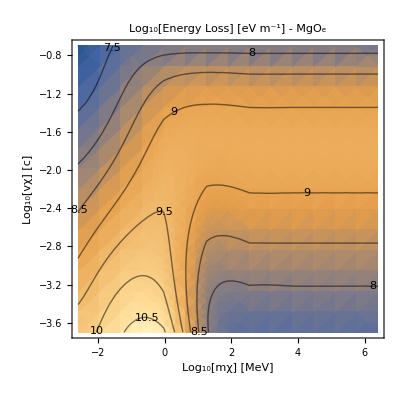

```mathematica
EnergyLoss`PlotEL[MgOλeDictSI,"MgO_e"]
```

### Compute Interaction Lengths - Post Mistake

#### Load Parameters

```mathematica
FeTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/FeTotalparams"];
SiO2Totalparams= ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/SiO2Totalparams"];
MgOTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/MgOTotalparams"];
```

#### Debug

```mathematica
EnergyLossMSIFitEnhanced[2.5 10^5("JpereV")/("c")^2/.SIConstRepl,2 10^-3"c" /.SIConstRepl,FeTotalparamscoreT[[1]],0]
```

For mχ = 4.45×10^-31 , vχ = 600000
L:	-0.0735798 
Prefactor:	3.97147×10^10
dEdr:	-2.9222×10^9

<|mχ→4.45×10^-31,vχ→600000,fitparams→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→1.038×10^29,qF→1.45392×10^10,vF→1.68373×10^6,μ→1.29132×10^-18,ωp→1.81874×10^16,α→1/137,χ→0.643411,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→322.436,nI→1.2975×10^28,Z→8,M→9.27329×10^-26,EF→1.29132×10^-18,ωi→1.81874×10^16,νi→1.75116×10^16,Ai→0.209474,ωedgei→6.04519×10^14},L→-0.0735798,Prefactor→3.97147×10^10,dEdr→-2.9222×10^9|>

```mathematica
EnergyLossMSIFitEnhanced[2.5 10^5("JpereV")/("c")^2/.SIConstRepl,2 10^-3"c" /.SIConstRepl,FeTotalparamscoreT[[1]],0]
```

For mχ = 4.45×10^-31 , vχ = 600000
L:	-0.0735798 
Prefactor:	3.97147×10^10
dEdr:	-2.9222×10^9

<|mχ→4.45×10^-31,vχ→600000,fitparams→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→1.038×10^29,qF→1.45392×10^10,vF→1.68373×10^6,μ→1.29132×10^-18,ωp→1.81874×10^16,α→1/137,χ→0.643411,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→322.436,nI→1.2975×10^28,Z→8,M→9.27329×10^-26,EF→1.29132×10^-18,ωi→1.81874×10^16,νi→1.75116×10^16,Ai→0.209474,ωedgei→6.04519×10^14},L→-0.0735798,Prefactor→3.97147×10^10,dEdr→-2.9222×10^9|>

```mathematica
zMIntegralFitEnhanced[2.5 10^5("JpereV")/("c")^2/.SIConstRepl,2 10^-3"c" /.SIConstRepl,Join[FeTotalparamscoreT[[1]],{"ωBG"->0}],0]
```

-0.0735798

```mathematica
zMIntegralFitEnhanced[2.5 10^5("JpereV")/("c")^2/.SIConstRepl,2 10^-3"c" /.SIConstRepl,Join[FeTotalparamscoreT[[1]],{"ωBG"->0}],0]
```

-0.0735798

```mathematica
zMIntegralFitEnhanced[2.5 10^12("JpereV")/("c")^2/.SIConstRepl,2 10^-2"c" /.SIConstRepl,Join[FeTotalparamscoreT[[1]],{"ωBG"->0}],0]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.00028093}. NIntegrate obtained 0.520872 and 3.27274×10^-6 for the integral and error estimates.

0.520872

```mathematica
zMIntegralFitEnhanced[2.5 10^7("JpereV")/("c")^2/.SIConstRepl,2 10^-2"c" /.SIConstRepl,Join[FeTotalparamscoreT[[1]],{"ωBG"->0}],0]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.00028093}. NIntegrate obtained 0.519782 and 2.78758×10^-6 for the integral and error estimates.

0.519782

```mathematica
"EF"/.FeTotalparamscoreT[[1]]
```

1.29132×10^-18

```mathematica
1/2(2.5 10^5("JpereV")/("c")^2/.SIConstRepl)(2 10^-3"c" /.SIConstRepl)^2
```

8.01×10^-20

```mathematica
1/2(2.5 10^12("JpereV")/("c")^2/.SIConstRepl)(2 10^-3"c" /.SIConstRepl)^2
```

8.01×10^-13

```mathematica
1/2(2.5 10^7("JpereV")/("c")^2/.SIConstRepl)(2 10^-3"c" /.SIConstRepl)^2
```

8.01×10^-18

```mathematica
zMIntegralFitEnhanced[2.5 10^5("JpereV")/("c")^2/.SIConstRepl,2 10^-3"c" /.SIConstRepl,Join[FeTotalparamscoreT[[1]],{"ωBG"->0}],1]
```

0.0435137

```mathematica
zMIntegralFitEnhanced[2.5 10^5("JpereV")/("c")^2/.SIConstRepl,2 10^-3"c" /.SIConstRepl,Join[SiO2Totalparams[[1]],{"ωBG"->0}],-1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.00536725}. NIntegrate obtained 0.176791 and 0.00614536 for the integral and error estimates.

0.176791

```mathematica
zMIntegralFitEnhanced[2.5 10^5("JpereV")/("c")^2/.SIConstRepl,2 10^-3"c" /.SIConstRepl,Join[SiO2Totalparams[[1]],{"ωBG"->0}],0]
```

-0.0483825

Refine::fas: Warning: one or more assumptions evaluated to False.

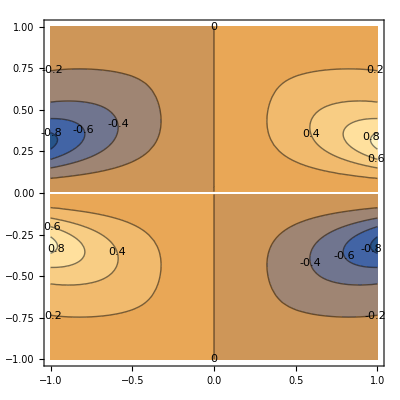

```mathematica
ContourPlot[ϵtest[u,z,SiO2Totalparams[[1]]],{u,-1,1},{z,-1,1},ContourLabels->True]
```

```mathematica
Integrate[DiracDelta[ω-q v u + (ℏ q^2)/(2 mχ)],{u,-1,1},Assumptions->{{ω, q,v,ℏ,mχ}∈ Reals,{q,v}>=0}]
```

1/(q v)(HeavisideTheta[-q v,-2 (q v+ω)-(q^2 ℏ)/mχ,-2 q v+2 ω+(q^2 ℏ)/mχ]+HeavisideTheta[q v,2 q v-2 ω-(q^2 ℏ)/mχ,2 q v+2 ω+(q^2 ℏ)/mχ])

```mathematica
Integrate[DiracDelta[ω-q v u + (ℏ q^2)/(2 mχ)],{u,-1,1},Assumptions->{{ω,q,v,ℏ,mχ}∈ Reals,{q,v}>=0}]
```

1/(q v)(HeavisideTheta[-q v,-2 (q v+ω)-(q^2 ℏ)/mχ,-2 q v+2 ω+(q^2 ℏ)/mχ]+HeavisideTheta[q v,2 q v-2 ω-(q^2 ℏ)/mχ,2 q v+2 ω+(q^2 ℏ)/mχ])

```mathematica
heavisidetest[q_,ω_,v_,mχ_,ℏ_]:=1/Abs[q v](HeavisideTheta[-q v,-2 (q v+ω)-(q^2 ℏ)/mχ,-2 q v+2 ω+(q^2 ℏ)/mχ]+HeavisideTheta[q v,2 q v-2 ω-(q^2 ℏ)/mχ,2 q v+2 ω+(q^2 ℏ)/mχ])
heavisidecurrenttest[q_,ω_,v_,mχ_,ℏ_]:=1/Abs[q v](HeavisideTheta[q v,2 q v-2 ω-(q^2 ℏ)/mχ,2 q v+2 ω+(q^2 ℏ)/mχ])
```

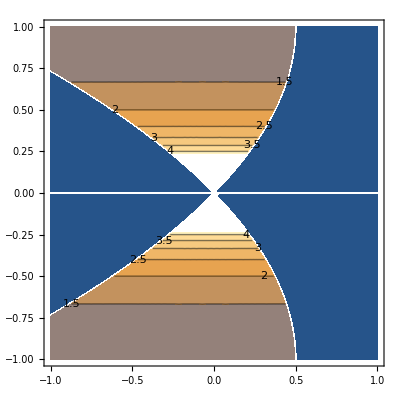

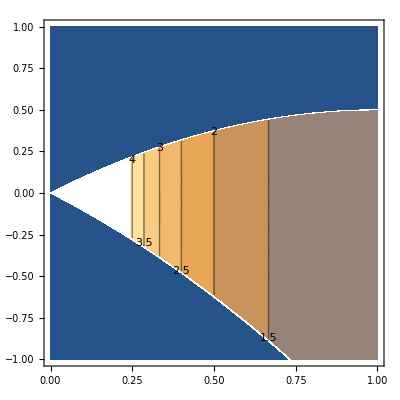

```mathematica
ContourPlot[heavisidetest[z,u,1,1,1],{u,-1,1},{z,-1,1},ContourLabels->True]
ContourPlot[heavisidecurrenttest[q,ω,1,1,1],{q,0,1},{ω,-1,1},ContourLabels->True]
```

```mathematica
EnergyLossMSIFitEnhanced[2.5 10^5("JpereV")/("c")^2/.SIConstRepl,2 10^-3"c" /.SIConstRepl,FeTotalparamscoreT[[1]],0]
```

For mχ = 4.45×10^-31 , vχ = 600000
L:	-0.0735798 
Prefactor:	3.97147×10^10
dEdr:	-2.9222×10^9

<|mχ→4.45×10^-31,vχ→600000,fitparams→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→1.038×10^29,qF→1.45392×10^10,vF→1.68373×10^6,μ→1.29132×10^-18,ωp→1.81874×10^16,α→1/137,χ→0.643411,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→322.436,nI→1.2975×10^28,Z→8,M→9.27329×10^-26,EF→1.29132×10^-18,ωi→1.81874×10^16,νi→1.75116×10^16,Ai→0.209474,ωedgei→6.04519×10^14},L→-0.0735798,Prefactor→3.97147×10^10,dEdr→-2.9222×10^9|>

```mathematica
EnergyLossMSIFitEnhanced[2.5 10^5("JpereV")/("c")^2/.SIConstRepl,2 10^-3"c" /.SIConstRepl,FeTotalparamscoreT[[1]],1]
```

For mχ = 4.45×10^-31 , vχ = 600000
L:	0.0435137 
Prefactor:	1.28051×10^12
dEdr:	5.57198×10^10

<|mχ→4.45×10^-31,vχ→600000,fitparams→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→1.038×10^29,qF→1.45392×10^10,vF→1.68373×10^6,μ→1.29132×10^-18,ωp→1.81874×10^16,α→1/137,χ→0.643411,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→322.436,nI→1.2975×10^28,Z→8,M→9.27329×10^-26,EF→1.29132×10^-18,ωi→1.81874×10^16,νi→1.75116×10^16,Ai→0.209474,ωedgei→6.04519×10^14},L→0.0435137,Prefactor→1.28051×10^12,dEdr→5.57198×10^10|>

#### Run Iron

```mathematica
FeTotalparamscoreT={{},{},{},{},{},{}};
Do[FeTotalparamscoreT[[i]]=Utilities`ReplaceParams[FeTotalparams[[i]],βcore,"β"],{i,Length[FeTotalparams]}];
```

```mathematica
FeλeDictSI= EnergyLossTableAndInterFITTotalParamsEnhanced[{2.5 10^3,2.5 10^12} ("JpereV")/("c")^2/.SIConstRepl,{2 10^-4,2 10^-1} "c" /.SIConstRepl,<|"mχ"->8,"vχ"->4|>,FeTotalparamscoreT,True,"FeλeDictSI",0]
```

1 of 32

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.000281647}. NIntegrate obtained -0.000827881 and 7.79925×10^-8 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000
L:	-0.000827881 
Prefactor:	3.97147×10^12
dEdr:	-3.2879×10^9

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0000909286}. NIntegrate obtained -0.000781284 and 4.1333×10^-9 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000
L:	-0.000781284 
Prefactor:	1.99412×10^12
dEdr:	-1.55797×10^9

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.00013778}. NIntegrate obtained -0.00054703 and 5.12677×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

For mχ = 4.45×10^-33 , vχ = 60000
L:	-0.00054703 
Prefactor:	1.90346×10^13
dEdr:	-1.04125×10^10

For mχ = 4.45×10^-33 , vχ = 60000
L:	-0.000230068 
Prefactor:	4.34962×10^13
dEdr:	-1.00071×10^10

For mχ = 4.45×10^-33 , vχ = 60000
L:	-0.0000325126 
Prefactor:	5.18691×10^12
dEdr:	-1.6864×10^8

For mχ = 4.45×10^-33 , vχ = 60000
L:	-4.99748×10^-6 
Prefactor:	1.39275×10^11
dEdr:	-696025.

dEdr total: -2.54348×10^10

2 of 32

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

For mχ = 4.45×10^-33 , vχ = 600000
L:	-0.00827812 
Prefactor:	3.97147×10^10
dEdr:	-3.28763×10^8

For mχ = 4.45×10^-33 , vχ = 600000
L:	-0.00781231 
Prefactor:	1.99412×10^10
dEdr:	-1.55787×10^8

For mχ = 4.45×10^-33 , vχ = 600000
L:	-0.00547011 
Prefactor:	1.90346×10^11
dEdr:	-1.04121×10^9

For mχ = 4.45×10^-33 , vχ = 600000
L:	-0.00230059 
Prefactor:	4.34962×10^11
dEdr:	-1.00067×10^9

For mχ = 4.45×10^-33 , vχ = 600000
L:	-0.000325126 
Prefactor:	5.18691×10^10
dEdr:	-1.6864×10^7

For mχ = 4.45×10^-33 , vχ = 600000
L:	-0.0000499748 
Prefactor:	1.39275×10^9
dEdr:	-69602.5

dEdr total: -2.54336×10^9

3 of 32

For mχ = 4.45×10^-33 , vχ = 6000000
L:	-0.0813722 
Prefactor:	3.97147×10^8
dEdr:	-3.23167×10^7

For mχ = 4.45×10^-33 , vχ = 6000000
L:	-0.077541 
Prefactor:	1.99412×10^8
dEdr:	-1.54626×10^7

For mχ = 4.45×10^-33 , vχ = 6000000
L:	-0.0543955 
Prefactor:	1.90346×10^9
dEdr:	-1.03539×10^8

For mχ = 4.45×10^-33 , vχ = 6000000
L:	-0.0229477 
Prefactor:	4.34962×10^9
dEdr:	-9.98138×10^7

For mχ = 4.45×10^-33 , vχ = 6000000
L:	-0.00325065 
Prefactor:	5.18691×10^8
dEdr:	-1.68609×10^6

For mχ = 4.45×10^-33 , vχ = 6000000
L:	-0.00049974 
Prefactor:	1.39275×10^7
dEdr:	-6960.13

dEdr total: -2.52826×10^8

4 of 32

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.60718 
Prefactor:	3.97147×10^6
dEdr:	2.4114×10^6

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.495995 
Prefactor:	1.99412×10^6
dEdr:	989073.

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.24579 
Prefactor:	1.90346×10^7
dEdr:	4.6785×10^6

For mχ = 4.45×10^-33 , vχ = 60000000
L:	-0.113308 
Prefactor:	4.34962×10^7
dEdr:	-4.92847×10^6

For mχ = 4.45×10^-33 , vχ = 60000000
L:	-0.031822 
Prefactor:	5.18691×10^6
dEdr:	-165058.

For mχ = 4.45×10^-33 , vχ = 60000000
L:	-0.00498841 
Prefactor:	139275.
dEdr:	-694.762

dEdr total: 2.98475×10^6

5 of 32

For mχ = 8.5916×10^-32 , vχ = 60000
L:	-0.00358022 
Prefactor:	3.97147×10^12
dEdr:	-1.42188×10^10

For mχ = 8.5916×10^-32 , vχ = 60000
L:	-0.00334347 
Prefactor:	1.99412×10^12
dEdr:	-6.66727×10^9

For mχ = 8.5916×10^-32 , vχ = 60000
L:	-0.00233743 
Prefactor:	1.90346×10^13
dEdr:	-4.4492×10^10

For mχ = 8.5916×10^-32 , vχ = 60000
L:	-0.000977712 
Prefactor:	4.34962×10^13
dEdr:	-4.25267×10^10

For mχ = 8.5916×10^-32 , vχ = 60000
L:	-0.000129283 
Prefactor:	5.18691×10^12
dEdr:	-6.7058×10^8

For mχ = 8.5916×10^-32 , vχ = 60000
L:	-0.0000167278 
Prefactor:	1.39275×10^11
dEdr:	-2.32977×10^6

dEdr total: -1.08578×10^11

6 of 32

For mχ = 8.5916×10^-32 , vχ = 600000
L:	-0.0356773 
Prefactor:	3.97147×10^10
dEdr:	-1.41691×10^9

For mχ = 8.5916×10^-32 , vχ = 600000
L:	-0.0333778 
Prefactor:	1.99412×10^10
dEdr:	-6.65594×10^8

For mχ = 8.5916×10^-32 , vχ = 600000
L:	-0.0233449 
Prefactor:	1.90346×10^11
dEdr:	-4.44361×10^9

For mχ = 8.5916×10^-32 , vχ = 600000
L:	-0.00977156 
Prefactor:	4.34962×10^11
dEdr:	-4.25025×10^9

For mχ = 8.5916×10^-32 , vχ = 600000
L:	-0.00129277 
Prefactor:	5.18691×10^10
dEdr:	-6.70548×10^7

For mχ = 8.5916×10^-32 , vχ = 600000
L:	-0.000167278 
Prefactor:	1.39275×10^9
dEdr:	-232976.

dEdr total: -1.08437×10^10

7 of 32

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	-0.139594 
Prefactor:	3.97147×10^8
dEdr:	-5.54395×10^7

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	-0.261599 
Prefactor:	1.99412×10^8
dEdr:	-5.21661×10^7

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	-0.196964 
Prefactor:	1.90346×10^9
dEdr:	-3.74912×10^8

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	-0.0910836 
Prefactor:	4.34962×10^9
dEdr:	-3.96179×10^8

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	-0.0128632 
Prefactor:	5.18691×10^8
dEdr:	-6.67202×10^6

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	-0.00167213 
Prefactor:	1.39275×10^7
dEdr:	-23288.7

dEdr total: -8.85392×10^8

8 of 32

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	1.0932 
Prefactor:	3.97147×10^6
dEdr:	4.34161×10^6

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	1.02783 
Prefactor:	1.99412×10^6
dEdr:	2.04961×10^6

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.792404 
Prefactor:	1.90346×10^7
dEdr:	1.50831×10^7

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.416368 
Prefactor:	4.34962×10^7
dEdr:	1.81104×10^7

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	-0.0243804 
Prefactor:	5.18691×10^6
dEdr:	-126459.

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	-0.0159609 
Prefactor:	139275.
dEdr:	-2222.95

dEdr total: 3.9456×10^7

9 of 32

For mχ = 1.65878×10^-30 , vχ = 60000
L:	-0.00451295 
Prefactor:	3.97147×10^12
dEdr:	-1.79231×10^10

For mχ = 1.65878×10^-30 , vχ = 60000
L:	-0.00332981 
Prefactor:	1.99412×10^12
dEdr:	-6.64004×10^9

For mχ = 1.65878×10^-30 , vχ = 60000
L:	-0.00248288 
Prefactor:	1.90346×10^13
dEdr:	-4.72606×10^10

For mχ = 1.65878×10^-30 , vχ = 60000
L:	-0.00108807 
Prefactor:	4.34962×10^13
dEdr:	-4.7327×10^10

For mχ = 1.65878×10^-30 , vχ = 60000
L:	-0.0000777499 
Prefactor:	5.18691×10^12
dEdr:	-4.03282×10^8

For mχ = 1.65878×10^-30 , vχ = 60000
L:	-5.35502×10^-6 
Prefactor:	1.39275×10^11
dEdr:	-745822.

dEdr total: -1.19555×10^11

10 of 32

For mχ = 1.65878×10^-30 , vχ = 600000
L:	-0.0422054 
Prefactor:	3.97147×10^10
dEdr:	-1.67617×10^9

For mχ = 1.65878×10^-30 , vχ = 600000
L:	-0.032804 
Prefactor:	1.99412×10^10
dEdr:	-6.5415×10^8

For mχ = 1.65878×10^-30 , vχ = 600000
L:	-0.0245065 
Prefactor:	1.90346×10^11
dEdr:	-4.66471×10^9

For mχ = 1.65878×10^-30 , vχ = 600000
L:	-0.0108087 
Prefactor:	4.34962×10^11
dEdr:	-4.70135×10^9

For mχ = 1.65878×10^-30 , vχ = 600000
L:	-0.000777371 
Prefactor:	5.18691×10^10
dEdr:	-4.03216×10^7

For mχ = 1.65878×10^-30 , vχ = 600000
L:	-0.0000535499 
Prefactor:	1.39275×10^9
dEdr:	-74581.8

dEdr total: -1.17368×10^10

11 of 32

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.490047 
Prefactor:	3.97147×10^8
dEdr:	1.94621×10^8

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.411155 
Prefactor:	1.99412×10^8
dEdr:	8.19893×10^7

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.26612 
Prefactor:	1.90346×10^9
dEdr:	5.06547×10^8

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.0307228 
Prefactor:	4.34962×10^9
dEdr:	1.33633×10^8

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	-0.00702994 
Prefactor:	5.18691×10^8
dEdr:	-3.64637×10^6

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	-0.000531287 
Prefactor:	1.39275×10^7
dEdr:	-7399.51

dEdr total: 9.13136×10^8

12 of 32

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	1.10305 
Prefactor:	3.97147×10^6
dEdr:	4.38073×10^6

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	1.03997 
Prefactor:	1.99412×10^6
dEdr:	2.07382×10^6

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.808381 
Prefactor:	1.90346×10^7
dEdr:	1.53872×10^7

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.447356 
Prefactor:	4.34962×10^7
dEdr:	1.94583×10^7

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.108554 
Prefactor:	5.18691×10^6
dEdr:	563060.

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	-0.00109138 
Prefactor:	139275.
dEdr:	-152.003

dEdr total: 4.18629×10^7

13 of 32

For mχ = 3.2026×10^-29 , vχ = 60000
L:	0.00126984 
Prefactor:	3.97147×10^12
dEdr:	5.04314×10^9

For mχ = 3.2026×10^-29 , vχ = 60000
L:	0.000348538 
Prefactor:	1.99412×10^12
dEdr:	6.95026×10^8

For mχ = 3.2026×10^-29 , vχ = 60000
L:	0.000146032 
Prefactor:	1.90346×10^13
dEdr:	2.77965×10^9

For mχ = 3.2026×10^-29 , vχ = 60000
L:	-7.48662×10^-6 
Prefactor:	4.34962×10^13
dEdr:	-3.25639×10^8

For mχ = 3.2026×10^-29 , vχ = 60000
L:	-3.86309×10^-6 
Prefactor:	5.18691×10^12
dEdr:	-2.00375×10^7

For mχ = 3.2026×10^-29 , vχ = 60000
L:	-2.81837×10^-7 
Prefactor:	1.39275×10^11
dEdr:	-39252.9

dEdr total: 8.17209×10^9

14 of 32

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.0235445 
Prefactor:	3.97147×10^10
dEdr:	9.35065×10^8

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.00896567 
Prefactor:	1.99412×10^10
dEdr:	1.78786×10^8

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.00486966 
Prefactor:	1.90346×10^11
dEdr:	9.26919×10^8

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.000837656 
Prefactor:	4.34962×10^11
dEdr:	3.64348×10^8

For mχ = 3.2026×10^-29 , vχ = 600000
L:	-0.0000277947 
Prefactor:	5.18691×10^10
dEdr:	-1.44169×10^6

For mχ = 3.2026×10^-29 , vχ = 600000
L:	-2.71616×10^-6 
Prefactor:	1.39275×10^9
dEdr:	-3782.93

dEdr total: 2.40367×10^9

15 of 32

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.519355 
Prefactor:	3.97147×10^8
dEdr:	2.0626×10^8

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.448355 
Prefactor:	1.99412×10^8
dEdr:	8.94074×10^7

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.318281 
Prefactor:	1.90346×10^9
dEdr:	6.05833×10^8

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.111837 
Prefactor:	4.34962×10^9
dEdr:	4.86448×10^8

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.00209938 
Prefactor:	5.18691×10^8
dEdr:	1.08893×10^6

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.0000199647 
Prefactor:	1.39275×10^7
dEdr:	278.059

dEdr total: 1.38904×10^9

16 of 32

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	1.10335 
Prefactor:	3.97147×10^6
dEdr:	4.3819×10^6

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	1.04031 
Prefactor:	1.99412×10^6
dEdr:	2.0745×10^6

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.80883 
Prefactor:	1.90346×10^7
dEdr:	1.53957×10^7

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.448234 
Prefactor:	4.34962×10^7
dEdr:	1.94965×10^7

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.113641 
Prefactor:	5.18691×10^6
dEdr:	589447.

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.00581994 
Prefactor:	139275.
dEdr:	810.573

dEdr total: 4.19389×10^7

17 of 32

For mχ = 6.18325×10^-28 , vχ = 60000
L:	0.00159661 
Prefactor:	3.97147×10^12
dEdr:	6.3409×10^9

For mχ = 6.18325×10^-28 , vχ = 60000
L:	0.000543888 
Prefactor:	1.99412×10^12
dEdr:	1.08458×10^9

For mχ = 6.18325×10^-28 , vχ = 60000
L:	0.000292261 
Prefactor:	1.90346×10^13
dEdr:	5.56306×10^9

For mχ = 6.18325×10^-28 , vχ = 60000
L:	0.0000561258 
Prefactor:	4.34962×10^13
dEdr:	2.44126×10^9

For mχ = 6.18325×10^-28 , vχ = 60000
L:	2.32352×10^-7 
Prefactor:	5.18691×10^12
dEdr:	1.20519×10^6

For mχ = 6.18325×10^-28 , vχ = 60000
L:	-1.0165×10^-8 
Prefactor:	1.39275×10^11
dEdr:	-1415.73

dEdr total: 1.5431×10^10

18 of 32

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.0276482 
Prefactor:	3.97147×10^10
dEdr:	1.09804×10^9

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.0115479 
Prefactor:	1.99412×10^10
dEdr:	2.30279×10^8

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.00679562 
Prefactor:	1.90346×10^11
dEdr:	1.29352×10^9

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.00168928 
Prefactor:	4.34962×10^11
dEdr:	7.34772×10^8

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.0000256712 
Prefactor:	5.18691×10^10
dEdr:	1.33154×10^6

For mχ = 6.18325×10^-28 , vχ = 600000
L:	4.09482×10^-7 
Prefactor:	1.39275×10^9
dEdr:	570.308

dEdr total: 3.35794×10^9

19 of 32

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.520796 
Prefactor:	3.97147×10^8
dEdr:	2.06833×10^8

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.45018 
Prefactor:	1.99412×10^8
dEdr:	8.97714×10^7

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.320831 
Prefactor:	1.90346×10^9
dEdr:	6.10688×10^8

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.116085 
Prefactor:	4.34962×10^9
dEdr:	5.04926×10^8

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.00268336 
Prefactor:	5.18691×10^8
dEdr:	1.39184×10^6

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.0000589051 
Prefactor:	1.39275×10^7
dEdr:	820.402

dEdr total: 1.41361×10^9

20 of 32

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	1.10335 
Prefactor:	3.97147×10^6
dEdr:	4.38191×10^6

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	1.04033 
Prefactor:	1.99412×10^6
dEdr:	2.07453×10^6

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.808851 
Prefactor:	1.90346×10^7
dEdr:	1.53961×10^7

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.448277 
Prefactor:	4.34962×10^7
dEdr:	1.94983×10^7

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.113892 
Prefactor:	5.18691×10^6
dEdr:	590748.

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.00620788 
Prefactor:	139275.
dEdr:	864.604

dEdr total: 4.19425×10^7

21 of 32

For mχ = 1.1938×10^-26 , vχ = 60000
L:	0.0016145 
Prefactor:	3.97147×10^12
dEdr:	6.41195×10^9

For mχ = 1.1938×10^-26 , vχ = 60000
L:	0.000554787 
Prefactor:	1.99412×10^12
dEdr:	1.10631×10^9

For mχ = 1.1938×10^-26 , vχ = 60000
L:	0.000300631 
Prefactor:	1.90346×10^13
dEdr:	5.72238×10^9

For mχ = 1.1938×10^-26 , vχ = 60000
L:	0.000060013 
Prefactor:	4.34962×10^13
dEdr:	2.61034×10^9

For mχ = 1.1938×10^-26 , vχ = 60000
L:	5.10069×10^-7 
Prefactor:	5.18691×10^12
dEdr:	2.64568×10^6

For mχ = 1.1938×10^-26 , vχ = 60000
L:	6.99949×10^-9 
Prefactor:	1.39275×10^11
dEdr:	974.855

dEdr total: 1.58536×10^10

22 of 32

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.0278626 
Prefactor:	3.97147×10^10
dEdr:	1.10656×10^9

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.0116832 
Prefactor:	1.99412×10^10
dEdr:	2.32978×10^8

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00689681 
Prefactor:	1.90346×10^11
dEdr:	1.31278×10^9

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00173451 
Prefactor:	4.34962×10^11
dEdr:	7.54445×10^8

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.0000287484 
Prefactor:	5.18691×10^10
dEdr:	1.49115×10^6

For mχ = 1.1938×10^-26 , vχ = 600000
L:	6.14897×10^-7 
Prefactor:	1.39275×10^9
dEdr:	856.399

dEdr total: 3.40825×10^9

23 of 32

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.520871 
Prefactor:	3.97147×10^8
dEdr:	2.06862×10^8

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.450275 
Prefactor:	1.99412×10^8
dEdr:	8.97902×10^7

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.320963 
Prefactor:	1.90346×10^9
dEdr:	6.10939×10^8

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.116304 
Prefactor:	4.34962×10^9
dEdr:	5.05879×10^8

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.00271392 
Prefactor:	5.18691×10^8
dEdr:	1.40769×10^6

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.0000610006 
Prefactor:	1.39275×10^7
dEdr:	849.587

dEdr total: 1.41488×10^9

24 of 32

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	1.10333 
Prefactor:	3.97147×10^6
dEdr:	4.38184×10^6

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	1.04033 
Prefactor:	1.99412×10^6
dEdr:	2.07454×10^6

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.808855 
Prefactor:	1.90346×10^7
dEdr:	1.53962×10^7

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.44828 
Prefactor:	4.34962×10^7
dEdr:	1.94985×10^7

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.113905 
Prefactor:	5.18691×10^6
dEdr:	590815.

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.00622803 
Prefactor:	139275.
dEdr:	867.411

dEdr total: 4.19427×10^7

25 of 32

For mχ = 2.30487×10^-25 , vχ = 60000
L:	0.00161543 
Prefactor:	3.97147×10^12
dEdr:	6.41564×10^9

For mχ = 2.30487×10^-25 , vχ = 60000
L:	0.000555354 
Prefactor:	1.99412×10^12
dEdr:	1.10744×10^9

For mχ = 2.30487×10^-25 , vχ = 60000
L:	0.000301067 
Prefactor:	1.90346×10^13
dEdr:	5.73069×10^9

For mχ = 2.30487×10^-25 , vχ = 60000
L:	0.0000602171 
Prefactor:	4.34962×10^13
dEdr:	2.61922×10^9

For mχ = 2.30487×10^-25 , vχ = 60000
L:	5.25286×10^-7 
Prefactor:	5.18691×10^12
dEdr:	2.72461×10^6

For mχ = 2.30487×10^-25 , vχ = 60000
L:	8.05591×10^-9 
Prefactor:	1.39275×10^11
dEdr:	1121.99

dEdr total: 1.58757×10^10

26 of 32

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.0278689 
Prefactor:	3.97147×10^10
dEdr:	1.10681×10^9

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.0116903 
Prefactor:	1.99412×10^10
dEdr:	2.33118×10^8

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00690205 
Prefactor:	1.90346×10^11
dEdr:	1.31378×10^9

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00173687 
Prefactor:	4.34962×10^11
dEdr:	7.5547×10^8

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.0000289093 
Prefactor:	5.18691×10^10
dEdr:	1.4995×10^6

For mχ = 2.30487×10^-25 , vχ = 600000
L:	6.25744×10^-7 
Prefactor:	1.39275×10^9
dEdr:	871.506

dEdr total: 3.41067×10^9

27 of 32

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.520873 
Prefactor:	3.97147×10^8
dEdr:	2.06863×10^8

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.45028 
Prefactor:	1.99412×10^8
dEdr:	8.97911×10^7

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.32097 
Prefactor:	1.90346×10^9
dEdr:	6.10952×10^8

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.116316 
Prefactor:	4.34962×10^9
dEdr:	5.05928×10^8

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.0027155 
Prefactor:	5.18691×10^8
dEdr:	1.40851×10^6

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.0000611093 
Prefactor:	1.39275×10^7
dEdr:	851.101

dEdr total: 1.41494×10^9

28 of 32

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	1.10338 
Prefactor:	3.97147×10^6
dEdr:	4.38203×10^6

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	1.04033 
Prefactor:	1.99412×10^6
dEdr:	2.07454×10^6

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.808854 
Prefactor:	1.90346×10^7
dEdr:	1.53962×10^7

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.44828 
Prefactor:	4.34962×10^7
dEdr:	1.94985×10^7

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.113906 
Prefactor:	5.18691×10^6
dEdr:	590819.

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.00622908 
Prefactor:	139275.
dEdr:	867.556

dEdr total: 4.19429×10^7

29 of 32

For mχ = 4.45×10^-24 , vχ = 60000
L:	0.00161548 
Prefactor:	3.97147×10^12
dEdr:	6.41583×10^9

For mχ = 4.45×10^-24 , vχ = 60000
L:	0.000555383 
Prefactor:	1.99412×10^12
dEdr:	1.1075×10^9

For mχ = 4.45×10^-24 , vχ = 60000
L:	0.00030109 
Prefactor:	1.90346×10^13
dEdr:	5.73111×10^9

For mχ = 4.45×10^-24 , vχ = 60000
L:	0.0000602277 
Prefactor:	4.34962×10^13
dEdr:	2.61967×10^9

For mχ = 4.45×10^-24 , vχ = 60000
L:	5.26076×10^-7 
Prefactor:	5.18691×10^12
dEdr:	2.72871×10^6

For mχ = 4.45×10^-24 , vχ = 60000
L:	8.11118×10^-9 
Prefactor:	1.39275×10^11
dEdr:	1129.69

dEdr total: 1.58769×10^10

30 of 32

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.0278743 
Prefactor:	3.97147×10^10
dEdr:	1.10702×10^9

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.0116906 
Prefactor:	1.99412×10^10
dEdr:	2.33125×10^8

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.00690233 
Prefactor:	1.90346×10^11
dEdr:	1.31383×10^9

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.001737 
Prefactor:	4.34962×10^11
dEdr:	7.55527×10^8

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.0000289178 
Prefactor:	5.18691×10^10
dEdr:	1.49994×10^6

For mχ = 4.45×10^-24 , vχ = 600000
L:	6.26306×10^-7 
Prefactor:	1.39275×10^9
dEdr:	872.289

dEdr total: 3.411×10^9

31 of 32

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.520872 
Prefactor:	3.97147×10^8
dEdr:	2.06863×10^8

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.45028 
Prefactor:	1.99412×10^8
dEdr:	8.97912×10^7

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.32097 
Prefactor:	1.90346×10^9
dEdr:	6.10953×10^8

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.116316 
Prefactor:	4.34962×10^9
dEdr:	5.05931×10^8

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.00271558 
Prefactor:	5.18691×10^8
dEdr:	1.40855×10^6

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.0000611149 
Prefactor:	1.39275×10^7
dEdr:	851.18

dEdr total: 1.41495×10^9

32 of 32

For mχ = 4.45×10^-24 , vχ = 60000000
L:	1.10335 
Prefactor:	3.97147×10^6
dEdr:	4.38194×10^6

For mχ = 4.45×10^-24 , vχ = 60000000
L:	1.04033 
Prefactor:	1.99412×10^6
dEdr:	2.07454×10^6

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.808853 
Prefactor:	1.90346×10^7
dEdr:	1.53962×10^7

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.44828 
Prefactor:	4.34962×10^7
dEdr:	1.94985×10^7

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.113906 
Prefactor:	5.18691×10^6
dEdr:	590819.

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.00622913 
Prefactor:	139275.
dEdr:	867.564

dEdr total: 4.19428×10^7

<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{-2.54348×10^10,-2.54336×10^9,-2.52826×10^8,2.98475×10^6},{-1.08578×10^11,-1.08437×10^10,-8.85392×10^8,3.9456×10^7},{-1.19555×10^11,-1.17368×10^10,9.13136×10^8,4.18629×10^7},{8.17209×10^9,2.40367×10^9,1.38904×10^9,4.19389×10^7},{1.5431×10^10,3.35794×10^9,1.41361×10^9,4.19425×10^7},{1.58536×10^10,3.40825×10^9,1.41488×10^9,4.19427×10^7},{1.58757×10^10,3.41067×10^9,1.41494×10^9,4.19429×10^7},{1.58769×10^10,3.411×10^9,1.41495×10^9,4.19428×10^7}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→1.038×10^29,qF→1.45392×10^10,vF→1.68373×10^6,μ→1.29132×10^-18,ωp→1.81874×10^16,α→1/137,χ→0.643411,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→322.436,nI→1.2975×10^28,Z→8,M→9.27329×10^-26,EF→1.29132×10^-18,ωi→1.81874×10^16,νi→1.75116×10^16,Ai→0.209474,ωedgei→6.04519×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→1.91532×10^29,qF→1.78329×10^10,vF→2.06517×10^6,μ→1.94267×10^-18,ωp→2.47055×10^16,α→1/137,χ→0.580962,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→485.073,nI→2.39415×10^28,Z→8,M→9.27329×10^-26,EF→1.94267×10^-18,ωi→2.47055×10^16,νi→8.99966×10^15,Ai→0.0699144,ωedgei→6.5887×10^12},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→4.34359×10^29,qF→2.34292×10^10,vF→2.71326×10^6,μ→3.35328×10^-18,ωp→3.72046×10^16,α→1/137,χ→0.506851,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→837.295,nI→5.42949×10^28,Z→8,M→9.27329×10^-26,EF→3.35328×10^-18,ωi→3.72046×10^16,νi→2.01886×10^16,Ai→0.386622,ωedgei→3.02977×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→3.17873×10^30,qF→4.54874×10^10,vF→5.26776×10^6,μ→1.26398×10^-17,ωp→1.00647×10^17,α→1/137,χ→0.363758,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→3156.08,nI→3.97341×10^29,Z→8,M→9.27329×10^-26,EF→1.26398×10^-17,ωi→1.00647×10^17,νi→9.30837×10^16,Ai→0.234383,ωedgei→1.51848×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→4.14995×10^32,qF→2.30757×10^11,vF→2.67232×10^7,μ→3.25286×10^-16,ωp→1.14999×10^18,α→1/137,χ→0.161503,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→81222.,nI→5.18743×10^31,Z→8,M→9.27329×10^-26,EF→3.25286×10^-16,ωi→1.14999×10^18,νi→7.408×10^17,Ai→0.00108607,ωedgei→1.09042×10^18},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→4.0004×10^34,qF→1.05805×10^12,vF→1.2253×10^8,μ→6.83868×10^-15,ωp→1.12908×10^19,α→1/137,χ→0.0754231,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→1.70758×10^6,nI→5.00049×10^33,Z→8,M→9.27329×10^-26,EF→6.83868×10^-15,ωi→1.12908×10^19,νi→5.21962×10^18,Ai→1.38712×10^-6,ωedgei→1.09893×10^19}},fname→FeλeDictSI,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{499.26,453.473,425.753,497.308},{48.0675,51.3419,323.55,512.681},{26.4143,55.7756,401.073,629.078},{84.0107,289.528,468.022,550.688},{181.624,339.779,382.467,542.52},{160.761,344.749,386.052,558.069},{160.555,494.41,452.345,509.47},{157.648,354.537,493.413,459.744}},totalTime→11294.2|>

#### Plot Iron

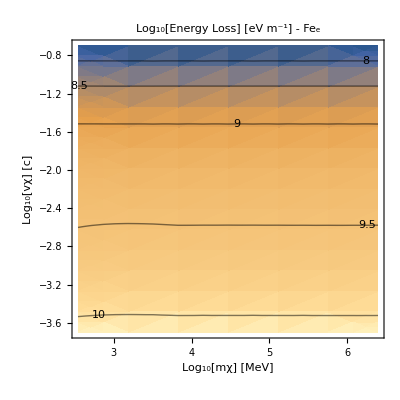

-Graphics-

```mathematica
EnergyLoss`PlotEL[FeλeDictSI,"Fe_e"]
```

#### Run SiO2

```mathematica
SiO2λeDictSI= EnergyLossTableAndInterFITTotalParamsEnhanced[{2.5 10^3,2.5 10^12} ("JpereV")/("c")^2/.SIConstRepl,{2 10^-4,2 10^-1} "c" /.SIConstRepl,<|"mχ"->8,"vχ"->4|>,SiO2Totalparams,True,"SiO2λeDictSI",0]
```

1 of 32

For mχ = 4.45×10^-33 , vχ = 60000
L:	-0.000590303 
Prefactor:	2.60571×10^13
dEdr:	-1.53816×10^10

For mχ = 4.45×10^-33 , vχ = 60000
L:	-0.000294259 
Prefactor:	1.19243×10^13
dEdr:	-3.50882×10^9

dEdr total: -1.88904×10^10

2 of 32

For mχ = 4.45×10^-33 , vχ = 600000
L:	-0.00590271 
Prefactor:	2.60571×10^11
dEdr:	-1.53807×10^9

For mχ = 4.45×10^-33 , vχ = 600000
L:	-0.0029425 
Prefactor:	1.19243×10^11
dEdr:	-3.50872×10^8

dEdr total: -1.88895×10^9

3 of 32

For mχ = 4.45×10^-33 , vχ = 6000000
L:	-0.0586776 
Prefactor:	2.60571×10^9
dEdr:	-1.52897×10^8

For mχ = 4.45×10^-33 , vχ = 6000000
L:	-0.0293392 
Prefactor:	1.19243×10^9
dEdr:	-3.49848×10^7

dEdr total: -1.87882×10^8

4 of 32

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.00013778}. NIntegrate obtained 0.23487 and 5.77541×10^-7 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.23487 
Prefactor:	2.60571×10^7
dEdr:	6.12003×10^6

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.00013778}. NIntegrate obtained -0.101242 and 5.32659×10^-7 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000000
L:	-0.101242 
Prefactor:	1.19243×10^7
dEdr:	-1.20723×10^6

dEdr total: 4.91279×10^6

5 of 32

For mχ = 8.5916×10^-32 , vχ = 60000
L:	-0.00252165 
Prefactor:	2.60571×10^13
dEdr:	-6.57068×10^10

For mχ = 8.5916×10^-32 , vχ = 60000
L:	-0.00124952 
Prefactor:	1.19243×10^13
dEdr:	-1.48996×10^10

dEdr total: -8.06064×10^10

6 of 32

For mχ = 8.5916×10^-32 , vχ = 600000
L:	-0.0251843 
Prefactor:	2.60571×10^11
dEdr:	-6.56229×10^9

For mχ = 8.5916×10^-32 , vχ = 600000
L:	-0.0124871 
Prefactor:	1.19243×10^11
dEdr:	-1.489×10^9

dEdr total: -8.05128×10^9

7 of 32

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	-0.209319 
Prefactor:	2.60571×10^9
dEdr:	-5.45424×10^8

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	-0.114981 
Prefactor:	1.19243×10^9
dEdr:	-1.37106×10^8

dEdr total: -6.8253×10^8

8 of 32

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.764297 
Prefactor:	2.60571×10^7
dEdr:	1.99153×10^7

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.000279499}. NIntegrate obtained 0.482578 and 1.24428×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.482578 
Prefactor:	1.19243×10^7
dEdr:	5.75439×10^6

dEdr total: 2.56697×10^7

9 of 32

For mχ = 1.65878×10^-30 , vχ = 60000
L:	-0.00287483 
Prefactor:	2.60571×10^13
dEdr:	-7.49096×10^10

For mχ = 1.65878×10^-30 , vχ = 60000
L:	-0.00137799 
Prefactor:	1.19243×10^13
dEdr:	-1.64315×10^10

dEdr total: -9.13411×10^10

10 of 32

For mχ = 1.65878×10^-30 , vχ = 600000
L:	-0.0281682 
Prefactor:	2.60571×10^11
dEdr:	-7.33982×10^9

For mχ = 1.65878×10^-30 , vχ = 600000
L:	-0.0136474 
Prefactor:	1.19243×10^11
dEdr:	-1.62735×10^9

dEdr total: -8.96717×10^9

11 of 32

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.25927 
Prefactor:	2.60571×10^9
dEdr:	6.75581×10^8

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.0586747 
Prefactor:	1.19243×10^9
dEdr:	6.99653×10^7

dEdr total: 7.45546×10^8

12 of 32

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.779967 
Prefactor:	2.60571×10^7
dEdr:	2.03237×10^7

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.50925 
Prefactor:	1.19243×10^7
dEdr:	6.07243×10^6

dEdr total: 2.63961×10^7

13 of 32

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

For mχ = 3.2026×10^-29 , vχ = 60000
L:	-0.00012695 
Prefactor:	2.60571×10^13
dEdr:	-3.30795×10^9

For mχ = 3.2026×10^-29 , vχ = 60000
L:	-0.000069674 
Prefactor:	1.19243×10^13
dEdr:	-8.30811×10^8

dEdr total: -4.13876×10^9

14 of 32

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.00341159 
Prefactor:	2.60571×10^11
dEdr:	8.8896×10^8

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.000770923 
Prefactor:	1.19243×10^11
dEdr:	9.19269×10^7

dEdr total: 9.80887×10^8

15 of 32

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.310104 
Prefactor:	2.60571×10^9
dEdr:	8.08041×10^8

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.14391 
Prefactor:	1.19243×10^9
dEdr:	1.71602×10^8

dEdr total: 9.79643×10^8

16 of 32

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.780408 
Prefactor:	2.60571×10^7
dEdr:	2.03352×10^7

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.510003 
Prefactor:	1.19243×10^7
dEdr:	6.08141×10^6

dEdr total: 2.64166×10^7

17 of 32

For mχ = 6.18325×10^-28 , vχ = 60000
L:	0.0000536523 
Prefactor:	2.60571×10^13
dEdr:	1.39802×10^9

For mχ = 6.18325×10^-28 , vχ = 60000
L:	0.0000150321 
Prefactor:	1.19243×10^13
dEdr:	1.79247×10^8

dEdr total: 1.57727×10^9

18 of 32

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.00549059 
Prefactor:	2.60571×10^11
dEdr:	1.43069×10^9

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.00180451 
Prefactor:	1.19243×10^11
dEdr:	2.15175×10^8

dEdr total: 1.64586×10^9

19 of 32

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.312594 
Prefactor:	2.60571×10^9
dEdr:	8.14528×10^8

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.148285 
Prefactor:	1.19243×10^9
dEdr:	1.76819×10^8

dEdr total: 9.91347×10^8

20 of 32

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.78043 
Prefactor:	2.60571×10^7
dEdr:	2.03357×10^7

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.51004 
Prefactor:	1.19243×10^7
dEdr:	6.08186×10^6

dEdr total: 2.64176×10^7

21 of 32

For mχ = 1.1938×10^-26 , vχ = 60000
L:	0.0000645198 
Prefactor:	2.60571×10^13
dEdr:	1.6812×10^9

For mχ = 1.1938×10^-26 , vχ = 60000
L:	0.0000204516 
Prefactor:	1.19243×10^13
dEdr:	2.43871×10^8

dEdr total: 1.92507×10^9

22 of 32

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00559972 
Prefactor:	2.60571×10^11
dEdr:	1.45912×10^9

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.0018592 
Prefactor:	1.19243×10^11
dEdr:	2.21696×10^8

dEdr total: 1.68082×10^9

23 of 32

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.312722 
Prefactor:	2.60571×10^9
dEdr:	8.14863×10^8

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.148511 
Prefactor:	1.19243×10^9
dEdr:	1.77088×10^8

dEdr total: 9.91951×10^8

24 of 32

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.78043 
Prefactor:	2.60571×10^7
dEdr:	2.03357×10^7

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.510042 
Prefactor:	1.19243×10^7
dEdr:	6.08188×10^6

dEdr total: 2.64176×10^7

25 of 32

For mχ = 2.30487×10^-25 , vχ = 60000
L:	0.000065087 
Prefactor:	2.60571×10^13
dEdr:	1.69598×10^9

For mχ = 2.30487×10^-25 , vχ = 60000
L:	0.0000207354 
Prefactor:	1.19243×10^13
dEdr:	2.47254×10^8

dEdr total: 1.94323×10^9

26 of 32

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00560538 
Prefactor:	2.60571×10^11
dEdr:	1.4606×10^9

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00186204 
Prefactor:	1.19243×10^11
dEdr:	2.22034×10^8

dEdr total: 1.68263×10^9

27 of 32

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.312729 
Prefactor:	2.60571×10^9
dEdr:	8.14881×10^8

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.148523 
Prefactor:	1.19243×10^9
dEdr:	1.77102×10^8

dEdr total: 9.91983×10^8

28 of 32

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.780431 
Prefactor:	2.60571×10^7
dEdr:	2.03358×10^7

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.510042 
Prefactor:	1.19243×10^7
dEdr:	6.08188×10^6

dEdr total: 2.64176×10^7

29 of 32

For mχ = 4.45×10^-24 , vχ = 60000
L:	0.0000651165 
Prefactor:	2.60571×10^13
dEdr:	1.69675×10^9

For mχ = 4.45×10^-24 , vχ = 60000
L:	0.0000207502 
Prefactor:	1.19243×10^13
dEdr:	2.47431×10^8

dEdr total: 1.94418×10^9

30 of 32

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.00560564 
Prefactor:	2.60571×10^11
dEdr:	1.46067×10^9

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.00186218 
Prefactor:	1.19243×10^11
dEdr:	2.22051×10^8

dEdr total: 1.68272×10^9

31 of 32

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.312729 
Prefactor:	2.60571×10^9
dEdr:	8.14881×10^8

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.148523 
Prefactor:	1.19243×10^9
dEdr:	1.77103×10^8

dEdr total: 9.91984×10^8

32 of 32

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.780431 
Prefactor:	2.60571×10^7
dEdr:	2.03358×10^7

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.510042 
Prefactor:	1.19243×10^7
dEdr:	6.08188×10^6

dEdr total: 2.64177×10^7

<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{-1.88904×10^10,-1.88895×10^9,-1.87882×10^8,4.91279×10^6},{-8.06064×10^10,-8.05128×10^9,-6.8253×10^8,2.56697×10^7},{-9.13411×10^10,-8.96717×10^9,7.45546×10^8,2.63961×10^7},{-4.13876×10^9,9.80887×10^8,9.79643×10^8,2.64166×10^7},{1.57727×10^9,1.64586×10^9,9.91347×10^8,2.64176×10^7},{1.92507×10^9,1.68082×10^9,9.91951×10^8,2.64176×10^7},{1.94323×10^9,1.68263×10^9,9.91983×10^8,2.64176×10^7},{1.94418×10^9,1.68272×10^9,9.91984×10^8,2.64177×10^7}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.07027×10^29,qF→2.2927×10^10,vF→2.65511×10^6,μ→3.21109×10^-18,ωp→3.60151×10^16,α→1/137,χ→0.512371,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→801.791,nI→5.08784×10^28,Z→8,M→9.27329×10^-26,EF→3.21109×10^-18,ωi→3.60151×10^16,νi→2.11534×10^16,Ai→0.552697,ωedgei→0},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→2.0121×10^30,qF→3.90562×10^10,vF→4.52297×10^6,μ→9.3183×10^-18,ωp→8.0075×10^16,α→1/137,χ→0.392567,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→2326.72,nI→2.51512×10^29,Z→8,M→9.27329×10^-26,EF→9.3183×10^-18,ωi→8.0075×10^16,νi→6.06034×10^16,Ai→0.0871584,ωedgei→0}},fname→SiO2λeDictSI,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{136.038,120.3,82.9105,166.946},{15.0242,22.7,39.3055,164.543},{8.27511,21.4427,135.417,275.156},{174.211,158.523,69.1168,219.397},{239.614,444.469,143.582,438.358},{507.16,424.618,128.024,580.02},{498.243,437.604,127.678,450.424},{504.69,425.533,139.81,384.407}},totalTime→7683.54|>

#### Plot SiO2

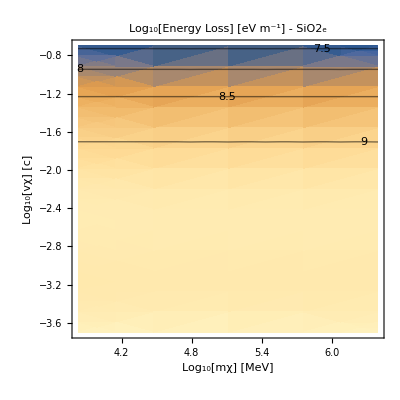

```mathematica
EnergyLoss`PlotEL[SiO2λeDictSI,"SiO2_e"]
```

#### Run MgO

```mathematica
(*MgOλeDictSI= EnergyLossTableAndInterFITTotalParamsEnhanced[{2.5 10^3,2.5 10^12} ("JpereV")/("c")^2/.SIConstRepl,{2 10^-4,2 10^-1} "c" /.SIConstRepl,<|"mχ"->8,"vχ"->4|>,MgOTotalparams,True,"MgOλeDictSI"]*)
```

```mathematica
MgOλeDictSI= EnergyLossTableAndInterFITTotalParamsEnhanced[{2.5 10^3,2.5 10^12} ("JpereV")/("c")^2/.SIConstRepl,{2 10^-4,2 10^-1} "c" /.SIConstRepl,<|"mχ"->8,"vχ"->4|>,MgOTotalparams,True,"MgOλeDictSI",0]
```

1 of 32

For mχ = 4.45×10^-33 , vχ = 60000
L:	-0.000969656 
Prefactor:	9.66968×10^11
dEdr:	-9.37626×10^8

For mχ = 4.45×10^-33 , vχ = 60000
L:	-0.000683201 
Prefactor:	7.79587×10^12
dEdr:	-5.32615×10^9

For mχ = 4.45×10^-33 , vχ = 60000
L:	-0.000630171 
Prefactor:	4.76717×10^12
dEdr:	-3.00413×10^9

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.00028093}. NIntegrate obtained -0.000283205 and 1.82238×10^-9 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000
L:	-0.000283205 
Prefactor:	4.98335×10^13
dEdr:	-1.41131×10^10

dEdr total: -2.3381×10^10

2 of 32

For mχ = 4.45×10^-33 , vχ = 600000
L:	-0.00969589 
Prefactor:	9.66968×10^9
dEdr:	-9.37561×10^7

For mχ = 4.45×10^-33 , vχ = 600000
L:	-0.00683171 
Prefactor:	7.79587×10^10
dEdr:	-5.32592×10^8

For mχ = 4.45×10^-33 , vχ = 600000
L:	-0.00630146 
Prefactor:	4.76717×10^10
dEdr:	-3.00401×10^8

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.000279499}. NIntegrate obtained -0.00283192 and 1.02781×10^-8 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 600000
L:	-0.00283192 
Prefactor:	4.98335×10^11
dEdr:	-1.41125×10^9

dEdr total: -2.338×10^9

3 of 32

For mχ = 4.45×10^-33 , vχ = 6000000
L:	-0.0962721 
Prefactor:	9.66968×10^7
dEdr:	-9.3092×10^6

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0354956}. NIntegrate obtained -0.0680171 and 3.36914×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

For mχ = 4.45×10^-33 , vχ = 6000000
L:	-0.0680171 
Prefactor:	7.79587×10^8
dEdr:	-5.30252×10^7

For mχ = 4.45×10^-33 , vχ = 6000000
L:	-0.0627666 
Prefactor:	4.76717×10^8
dEdr:	-2.99219×10^7

For mχ = 4.45×10^-33 , vχ = 6000000
L:	-0.0281801 
Prefactor:	4.98335×10^9
dEdr:	-1.40431×10^8

dEdr total: -2.32688×10^8

4 of 32

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.550917 
Prefactor:	966968.
dEdr:	532719.

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.318946 
Prefactor:	7.79587×10^6
dEdr:	2.48646×10^6

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.266855 
Prefactor:	4.76717×10^6
dEdr:	1.27214×10^6

For mχ = 4.45×10^-33 , vχ = 60000000
L:	-0.0263211 
Prefactor:	4.98335×10^7
dEdr:	-1.31167×10^6

dEdr total: 2.97965×10^6

5 of 32

For mχ = 8.5916×10^-32 , vχ = 60000
L:	-0.00412646 
Prefactor:	9.66968×10^11
dEdr:	-3.99015×10^9

For mχ = 8.5916×10^-32 , vχ = 60000
L:	-0.00288548 
Prefactor:	7.79587×10^12
dEdr:	-2.24948×10^10

For mχ = 8.5916×10^-32 , vχ = 60000
L:	-0.0026562 
Prefactor:	4.76717×10^12
dEdr:	-1.26625×10^10

For mχ = 8.5916×10^-32 , vχ = 60000
L:	-0.00121663 
Prefactor:	4.98335×10^13
dEdr:	-6.06291×10^10

dEdr total: -9.97767×10^10

6 of 32

For mχ = 8.5916×10^-32 , vχ = 600000
L:	-0.0411974 
Prefactor:	9.66968×10^9
dEdr:	-3.98366×10^8

For mχ = 8.5916×10^-32 , vχ = 600000
L:	-0.0288249 
Prefactor:	7.79587×10^10
dEdr:	-2.24716×10^9

For mχ = 8.5916×10^-32 , vχ = 600000
L:	-0.0265373 
Prefactor:	4.76717×10^10
dEdr:	-1.26508×10^9

For mχ = 8.5916×10^-32 , vχ = 600000
L:	-0.0121543 
Prefactor:	4.98335×10^11
dEdr:	-6.05693×10^9

dEdr total: -9.96753×10^9

7 of 32

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	-0.332715 
Prefactor:	9.66968×10^7
dEdr:	-3.21724×10^7

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	-0.256248 
Prefactor:	7.79587×10^8
dEdr:	-1.99768×10^8

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	-0.23909 
Prefactor:	4.76717×10^8
dEdr:	-1.13978×10^8

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	-0.104125 
Prefactor:	4.98335×10^9
dEdr:	-5.18892×10^8

dEdr total: -8.6481×10^8

8 of 32

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	1.06982 
Prefactor:	966968.
dEdr:	1.03448×10^6

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.873324 
Prefactor:	7.79587×10^6
dEdr:	6.80833×10^6

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.832401 
Prefactor:	4.76717×10^6
dEdr:	3.96819×10^6

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.442129 
Prefactor:	4.98335×10^7
dEdr:	2.20329×10^7

dEdr total: 3.38439×10^7

9 of 32

For mχ = 1.65878×10^-30 , vχ = 60000
L:	-0.00407681 
Prefactor:	9.66968×10^11
dEdr:	-3.94215×10^9

For mχ = 1.65878×10^-30 , vχ = 60000
L:	-0.00269954 
Prefactor:	7.79587×10^12
dEdr:	-2.10453×10^10

For mχ = 1.65878×10^-30 , vχ = 60000
L:	-0.00245085 
Prefactor:	4.76717×10^12
dEdr:	-1.16836×10^10

For mχ = 1.65878×10^-30 , vχ = 60000
L:	-0.00183602 
Prefactor:	4.98335×10^13
dEdr:	-9.14952×10^10

dEdr total: -1.28166×10^11

10 of 32

For mχ = 1.65878×10^-30 , vχ = 600000
L:	-0.0399931 
Prefactor:	9.66968×10^9
dEdr:	-3.8672×10^8

For mχ = 1.65878×10^-30 , vχ = 600000
L:	-0.0267045 
Prefactor:	7.79587×10^10
dEdr:	-2.08185×10^9

For mχ = 1.65878×10^-30 , vχ = 600000
L:	-0.0242778 
Prefactor:	4.76717×10^10
dEdr:	-1.15736×10^9

For mχ = 1.65878×10^-30 , vχ = 600000
L:	-0.0178943 
Prefactor:	4.98335×10^11
dEdr:	-8.91734×10^9

dEdr total: -1.25433×10^10

11 of 32

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.439167 
Prefactor:	9.66968×10^7
dEdr:	4.24661×10^7

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.300959 
Prefactor:	7.79587×10^8
dEdr:	2.34624×10^8

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.270546 
Prefactor:	4.76717×10^8
dEdr:	1.28974×10^8

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.0885736 
Prefactor:	4.98335×10^9
dEdr:	4.41394×10^8

dEdr total: 8.47457×10^8

12 of 32

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	1.08106 
Prefactor:	966968.
dEdr:	1.04535×10^6

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.888352 
Prefactor:	7.79587×10^6
dEdr:	6.92548×10^6

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.848468 
Prefactor:	4.76717×10^6
dEdr:	4.04479×10^6

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.46682 
Prefactor:	4.98335×10^7
dEdr:	2.32633×10^7

dEdr total: 3.52789×10^7

13 of 32

For mχ = 3.2026×10^-29 , vχ = 60000
L:	-0.000151464 
Prefactor:	9.66968×10^11
dEdr:	-1.46461×10^8

For mχ = 3.2026×10^-29 , vχ = 60000
L:	-0.000115126 
Prefactor:	7.79587×10^12
dEdr:	-8.97507×10^8

For mχ = 3.2026×10^-29 , vχ = 60000
L:	-0.000106844 
Prefactor:	4.76717×10^12
dEdr:	-5.09344×10^8

For mχ = 3.2026×10^-29 , vχ = 60000
L:	-0.0000969176 
Prefactor:	4.98335×10^13
dEdr:	-4.82975×10^9

dEdr total: -6.38306×10^9

14 of 32

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.00622458 
Prefactor:	9.66968×10^9
dEdr:	6.01897×10^7

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.00284575 
Prefactor:	7.79587×10^10
dEdr:	2.21851×10^8

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.00235317 
Prefactor:	4.76717×10^10
dEdr:	1.1218×10^8

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.00153754 
Prefactor:	4.98335×10^11
dEdr:	7.66211×10^8

dEdr total: 1.16043×10^9

15 of 32

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.473246 
Prefactor:	9.66968×10^7
dEdr:	4.57614×10^7

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.349623 
Prefactor:	7.79587×10^8
dEdr:	2.72562×10^8

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.323824 
Prefactor:	4.76717×10^8
dEdr:	1.54372×10^8

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.152326 
Prefactor:	4.98335×10^9
dEdr:	7.59092×10^8

dEdr total: 1.23179×10^9

16 of 32

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	1.08138 
Prefactor:	966968.
dEdr:	1.04566×10^6

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.888775 
Prefactor:	7.79587×10^6
dEdr:	6.92878×10^6

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.848919 
Prefactor:	4.76717×10^6
dEdr:	4.04694×10^6

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.467518 
Prefactor:	4.98335×10^7
dEdr:	2.32981×10^7

dEdr total: 3.53195×10^7

17 of 32

For mχ = 6.18325×10^-28 , vχ = 60000
L:	0.0000918255 
Prefactor:	9.66968×10^11
dEdr:	8.87923×10^7

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

For mχ = 6.18325×10^-28 , vχ = 60000
L:	0.0000442587 
Prefactor:	7.79587×10^12
dEdr:	3.45035×10^8

For mχ = 6.18325×10^-28 , vχ = 60000
L:	0.000037302 
Prefactor:	4.76717×10^12
dEdr:	1.77825×10^8

For mχ = 6.18325×10^-28 , vχ = 60000
L:	0.0000273 
Prefactor:	4.98335×10^13
dEdr:	1.36046×10^9

dEdr total: 1.97211×10^9

18 of 32

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.00901566 
Prefactor:	9.66968×10^9
dEdr:	8.71785×10^7

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.00471346 
Prefactor:	7.79587×10^10
dEdr:	3.67455×10^8

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.00405336 
Prefactor:	4.76717×10^10
dEdr:	1.9323×10^8

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.00300654 
Prefactor:	4.98335×10^11
dEdr:	1.49827×10^9

dEdr total: 2.14613×10^9

19 of 32

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.474921 
Prefactor:	9.66968×10^7
dEdr:	4.59233×10^7

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.352 
Prefactor:	7.79587×10^8
dEdr:	2.74415×10^8

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.326417 
Prefactor:	4.76717×10^8
dEdr:	1.55608×10^8

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.155606 
Prefactor:	4.98335×10^9
dEdr:	7.75442×10^8

dEdr total: 1.25139×10^9

20 of 32

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	1.0814 
Prefactor:	966968.
dEdr:	1.04567×10^6

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.888796 
Prefactor:	7.79587×10^6
dEdr:	6.92894×10^6

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.848941 
Prefactor:	4.76717×10^6
dEdr:	4.04704×10^6

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.467556 
Prefactor:	4.98335×10^7
dEdr:	2.33×10^7

dEdr total: 3.53216×10^7

21 of 32

For mχ = 1.1938×10^-26 , vχ = 60000
L:	0.000105956 
Prefactor:	9.66968×10^11
dEdr:	1.02456×10^8

For mχ = 1.1938×10^-26 , vχ = 60000
L:	0.0000538392 
Prefactor:	7.79587×10^12
dEdr:	4.19723×10^8

For mχ = 1.1938×10^-26 , vχ = 60000
L:	0.0000460405 
Prefactor:	4.76717×10^12
dEdr:	2.19483×10^8

For mχ = 1.1938×10^-26 , vχ = 60000
L:	0.0000351091 
Prefactor:	4.98335×10^13
dEdr:	1.74961×10^9

dEdr total: 2.49127×10^9

22 of 32

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00916185 
Prefactor:	9.66968×10^9
dEdr:	8.85921×10^7

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00481155 
Prefactor:	7.79587×10^10
dEdr:	3.75103×10^8

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00414272 
Prefactor:	4.76717×10^10
dEdr:	1.9749×10^8

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00308407 
Prefactor:	4.98335×10^11
dEdr:	1.5369×10^9

dEdr total: 2.19809×10^9

23 of 32

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.475008 
Prefactor:	9.66968×10^7
dEdr:	4.59317×10^7

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.352121 
Prefactor:	7.79587×10^8
dEdr:	2.74509×10^8

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.326551 
Prefactor:	4.76717×10^8
dEdr:	1.55672×10^8

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.155776 
Prefactor:	4.98335×10^9
dEdr:	7.76289×10^8

dEdr total: 1.2524×10^9

24 of 32

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	1.0814 
Prefactor:	966968.
dEdr:	1.04568×10^6

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.888797 
Prefactor:	7.79587×10^6
dEdr:	6.92895×10^6

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.848943 
Prefactor:	4.76717×10^6
dEdr:	4.04705×10^6

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.467557 
Prefactor:	4.98335×10^7
dEdr:	2.33×10^7

dEdr total: 3.53217×10^7

25 of 32

For mχ = 2.30487×10^-25 , vχ = 60000
L:	0.000106692 
Prefactor:	9.66968×10^11
dEdr:	1.03168×10^8

For mχ = 2.30487×10^-25 , vχ = 60000
L:	0.000054339 
Prefactor:	7.79587×10^12
dEdr:	4.2362×10^8

For mχ = 2.30487×10^-25 , vχ = 60000
L:	0.0000464966 
Prefactor:	4.76717×10^12
dEdr:	2.21657×10^8

For mχ = 2.30487×10^-25 , vχ = 60000
L:	0.0000355177 
Prefactor:	4.98335×10^13
dEdr:	1.76997×10^9

dEdr total: 2.51842×10^9

26 of 32

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00916942 
Prefactor:	9.66968×10^9
dEdr:	8.86654×10^7

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00481664 
Prefactor:	7.79587×10^10
dEdr:	3.75499×10^8

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00414735 
Prefactor:	4.76717×10^10
dEdr:	1.97711×10^8

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00308809 
Prefactor:	4.98335×10^11
dEdr:	1.5389×10^9

dEdr total: 2.20078×10^9

27 of 32

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.475012 
Prefactor:	9.66968×10^7
dEdr:	4.59321×10^7

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.352128 
Prefactor:	7.79587×10^8
dEdr:	2.74514×10^8

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.326558 
Prefactor:	4.76717×10^8
dEdr:	1.55676×10^8

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.155785 
Prefactor:	4.98335×10^9
dEdr:	7.76332×10^8

dEdr total: 1.25245×10^9

28 of 32

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	1.0814 
Prefactor:	966968.
dEdr:	1.04568×10^6

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.888797 
Prefactor:	7.79587×10^6
dEdr:	6.92895×10^6

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.848943 
Prefactor:	4.76717×10^6
dEdr:	4.04705×10^6

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.467561 
Prefactor:	4.98335×10^7
dEdr:	2.33002×10^7

dEdr total: 3.53219×10^7

29 of 32

For mχ = 4.45×10^-24 , vχ = 60000
L:	0.00010673 
Prefactor:	9.66968×10^11
dEdr:	1.03205×10^8

For mχ = 4.45×10^-24 , vχ = 60000
L:	0.0000543648 
Prefactor:	7.79587×10^12
dEdr:	4.23821×10^8

For mχ = 4.45×10^-24 , vχ = 60000
L:	0.0000465203 
Prefactor:	4.76717×10^12
dEdr:	2.2177×10^8

For mχ = 4.45×10^-24 , vχ = 60000
L:	0.000035539 
Prefactor:	4.98335×10^13
dEdr:	1.77103×10^9

dEdr total: 2.51983×10^9

30 of 32

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.00916981 
Prefactor:	9.66968×10^9
dEdr:	8.86692×10^7

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.0048169 
Prefactor:	7.79587×10^10
dEdr:	3.7552×10^8

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.00414759 
Prefactor:	4.76717×10^10
dEdr:	1.97723×10^8

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.00308831 
Prefactor:	4.98335×10^11
dEdr:	1.53901×10^9

dEdr total: 2.20092×10^9

31 of 32

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.475012 
Prefactor:	9.66968×10^7
dEdr:	4.59322×10^7

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.352128 
Prefactor:	7.79587×10^8
dEdr:	2.74514×10^8

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.326558 
Prefactor:	4.76717×10^8
dEdr:	1.55676×10^8

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.155786 
Prefactor:	4.98335×10^9
dEdr:	7.76335×10^8

dEdr total: 1.25246×10^9

32 of 32

For mχ = 4.45×10^-24 , vχ = 60000000
L:	1.0814 
Prefactor:	966968.
dEdr:	1.04568×10^6

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.888797 
Prefactor:	7.79587×10^6
dEdr:	6.92895×10^6

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.848943 
Prefactor:	4.76717×10^6
dEdr:	4.04705×10^6

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.467557 
Prefactor:	4.98335×10^7
dEdr:	2.33×10^7

dEdr total: 3.53217×10^7

<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{-2.3381×10^10,-2.338×10^9,-2.32688×10^8,2.97965×10^6},{-9.97767×10^10,-9.96753×10^9,-8.6481×10^8,3.38439×10^7},{-1.28166×10^11,-1.25433×10^10,8.47457×10^8,3.52789×10^7},{-6.38306×10^9,1.16043×10^9,1.23179×10^9,3.53195×10^7},{1.97211×10^9,2.14613×10^9,1.25139×10^9,3.53216×10^7},{2.49127×10^9,2.19809×10^9,1.2524×10^9,3.53217×10^7},{2.51842×10^9,2.20078×10^9,1.25245×10^9,3.53219×10^7},{2.51983×10^9,2.20092×10^9,1.25246×10^9,3.53217×10^7}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.50385×10^29,qF→1.64516×10^10,vF→1.90521×10^6,μ→1.65338×10^-18,ωp→2.18914×10^16,α→1/137,χ→0.604859,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→412.839,nI→1.87981×10^28,Z→8,M→9.27329×10^-26,EF→1.65338×10^-18,ωi→2.18914×10^16,νi→4.25006×10^15,Ai→0.039834,ωedgei→0},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→3.58115×10^29,qF→2.19692×10^10,vF→2.54418×10^6,μ→2.94839×10^-18,ωp→3.37819×10^16,α→1/137,χ→0.523421,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→736.197,nI→4.47644×10^28,Z→8,M→9.27329×10^-26,EF→2.94839×10^-18,ωi→3.37819×10^16,νi→5.06751×10^15,Ai→0.180092,ωedgei→0},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.37351×10^29,qF→2.34828×10^10,vF→2.71947×10^6,μ→3.36866×10^-18,ωp→3.73325×10^16,α→1/137,χ→0.506271,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→841.135,nI→5.46689×10^28,Z→8,M→9.27329×10^-26,EF→3.36866×10^-18,ωi→3.73325×10^16,νi→5.23006×10^15,Ai→0.0963866,ωedgei→0},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.61838×10^30,qF→3.63218×10^10,vF→4.20631×10^6,μ→8.05919×10^-18,ωp→7.18146×10^16,α→1/137,χ→0.407075,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→2012.33,nI→2.02298×10^29,Z→8,M→9.27329×10^-26,EF→8.05919×10^-18,ωi→7.18146×10^16,νi→1.12397×10^17,Ai→0.421157,ωedgei→0}},fname→MgOλeDictSI,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{197.646,182.329,174.354,397.265},{33.1394,49.3247,107.994,307.196},{17.2909,39.9811,184.61,429.421},{127.193,202.195,166.385,395.324},{282.14,176.944,137.171,401.293},{252.441,206.646,135.374,390.99},{303.777,224.758,178.736,502.238},{248.427,184.226,123.661,374.796}},totalTime→7135.27|>

#### Plot MgO

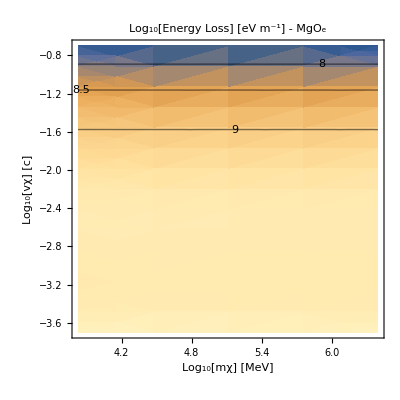

```mathematica
EnergyLoss`PlotEL[MgOλeDictSI,"MgO_e"]
```

### Test better plotting (for negative values in interaction length)

#### Load Interaction Dicts

```mathematica
FeλeDictSI = ReadIt[NotebookDirectory[]<>"FeλeDictSI"];
SiO2λeDictSI = ReadIt[NotebookDirectory[]<>"SiO2λeDictSI"];
MgOλeDictSI = ReadIt[NotebookDirectory[]<>"MgOλeDictSI"];
```

#### Define interpolation function with abs

```mathematica
Interpolate[outdict_,signed_:True]:=Module[{InterpolationTable},
InterpolationTable = Table[{{Log10[outdict["mχMesh"][[i, j]]], Log10[outdict["vχMesh"][[i, j]]]},
            If[signed, Sign[outdict["EnergyLossMesh"][[i, j]]],1]Log10[Abs[outdict["EnergyLossMesh"][[i, j]]]]}, {i, outdict["meshdims"][["mχ"]]}, {j, outdict["meshdims"][["vχ"]]
            }];
        Interpolation[Flatten[ InterpolationTable
            , 1]]
]
```

#### Run for Fe

```mathematica
fFesigned=Interpolate[FeλeDictSI]
SigneddictFe = FeλeDictSI;
SigneddictFe["f"]=fFesigned

fFeunsigned=Interpolate[FeλeDictSI,False]
unSigneddictFe = FeλeDictSI;
unSigneddictFe["f"]=fFeunsigned
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

«1 more identical outputs»

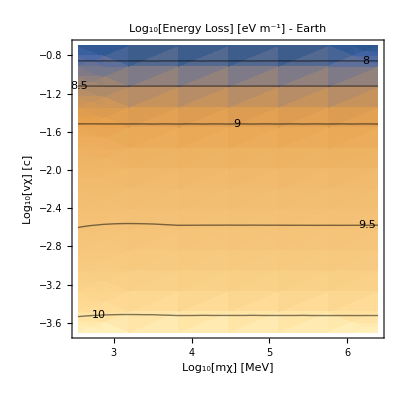

```mathematica
PlotEL[FeλeDictSI]
```

```mathematica
("EF")/("JpereV")/.FeTotalparams
```

{8.0607,12.1265,20.9318,78.9,2030.5,42688.4}

```mathematica
(10^-2.5"c")^2((6"m")/2)("JpereV")^-1/.SIConstRepl
(10^-3"c")^2((20 "m")/2)("JpereV")^-1/.SIConstRepl
(10^-3.5"c")^2((10"m")/2)("JpereV")^-1/.SIConstRepl
```

15.3539

5.11798

0.255899

Fe signed λ

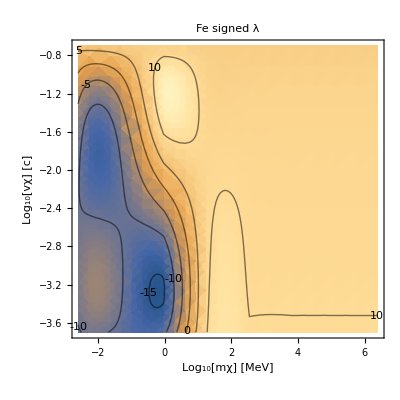

Fe unsigned λ

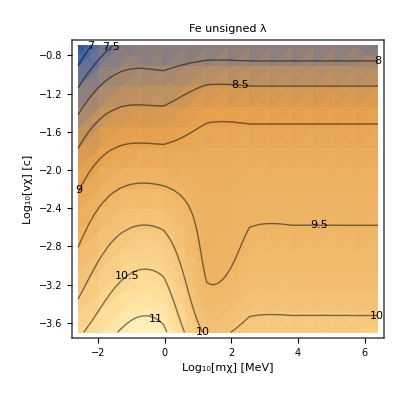

```mathematica
PlotEL[SigneddictFe,"",True,"Fe signed λ"]
PlotEL[unSigneddictFe,"",True,"Fe unsigned λ"]
```

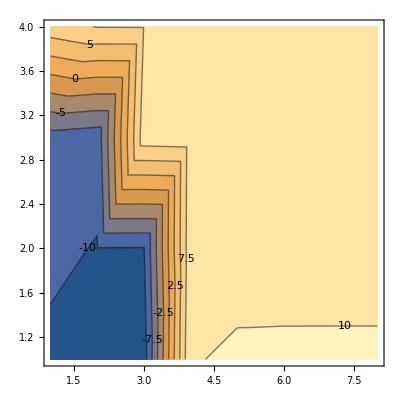

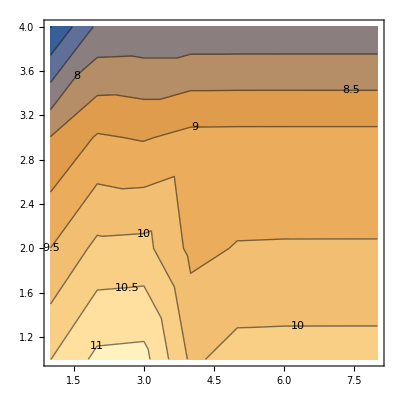

```mathematica
ListContourPlot[Table[Sign[FeλeDictSI["EnergyLossMesh"]][[i,j]]Abs[Log10[FeλeDictSI["EnergyLossMesh"]][[i,j]]],{j,FeλeDictSI["meshdims"]["vχ"]},{i,FeλeDictSI["meshdims"]["mχ"]}],ContourLabels->True]
ListContourPlot[Table[Abs[Log10[FeλeDictSI["EnergyLossMesh"]][[i,j]]],{j,FeλeDictSI["meshdims"]["vχ"]},{i,FeλeDictSI["meshdims"]["mχ"]}],ContourLabels->True]
```

#### Run for SiO2

```mathematica
fSiO2signed=Interpolate[SiO2λeDictSI]
SigneddictSiO2SiO2 = SiO2λeDictSI;
SigneddictSiO2SiO2["f"]=fSiO2signed

fSiO2unsigned=Interpolate[SiO2λeDictSI,False]
unSigneddictSiO2 = SiO2λeDictSI;
unSigneddictSiO2["f"]=fSiO2unsigned
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

«1 more identical outputs»

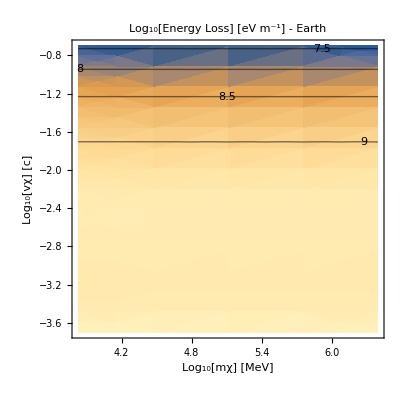

```mathematica
PlotEL[SiO2λeDictSI]
```

SiO2 signed λ

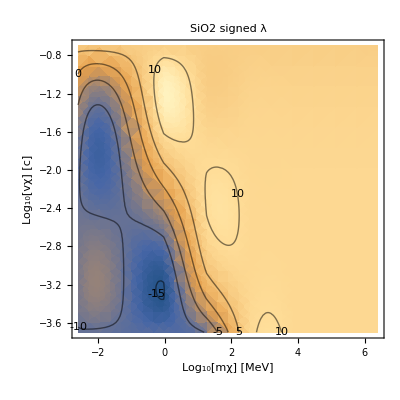

SiO2 signed λ

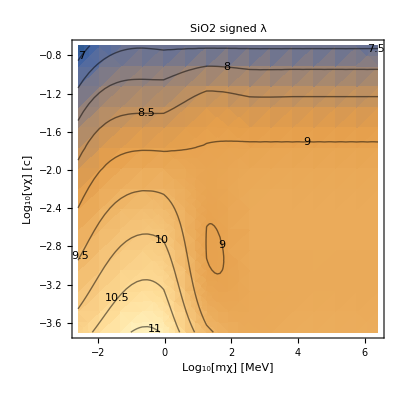

```mathematica
PlotEL[SigneddictSiO2,"",True,"SiO2 signed λ"]
PlotEL[unSigneddictSiO2,"",True,"SiO2 signed λ"]
```

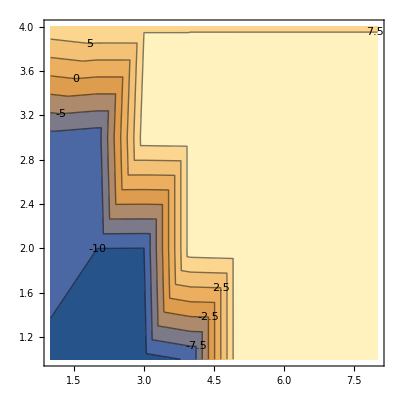

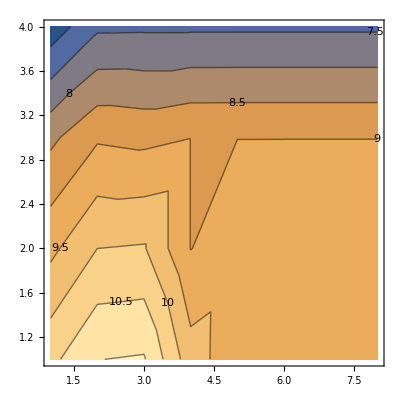

```mathematica
ListContourPlot[Table[Sign[SiO2λeDictSI["EnergyLossMesh"]][[i,j]]Abs[Log10[SiO2λeDictSI["EnergyLossMesh"]][[i,j]]],{j,SiO2λeDictSI["meshdims"]["vχ"]},{i,SiO2λeDictSI["meshdims"]["mχ"]}],ContourLabels->True]
ListContourPlot[Table[Abs[Log10[SiO2λeDictSI["EnergyLossMesh"]][[i,j]]],{j,SiO2λeDictSI["meshdims"]["vχ"]},{i,SiO2λeDictSI["meshdims"]["mχ"]}],ContourLabels->True]
```

#### Run for MgO

```mathematica
fMgOsigned=Interpolate[MgOλeDictSI]
Signeddict = MgOλeDictSI;
Signeddict["f"]=fMgOsigned

fMgOunsigned=Interpolate[MgOλeDictSI,False]
unSigneddict = MgOλeDictSI;
unSigneddict["f"]=fMgOunsigned
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

«1 more identical outputs»

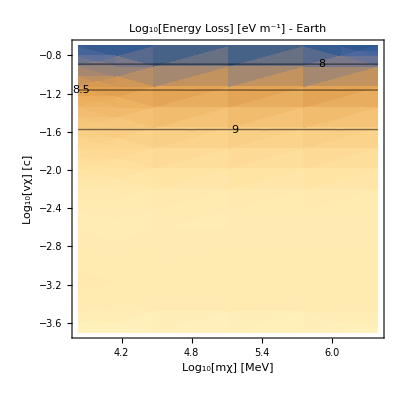

```mathematica
PlotEL[MgOλeDictSI]
```

SiO2 signed λ

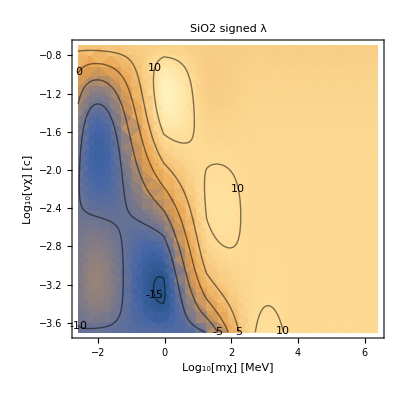

SiO2 signed λ

-Graphics-

```mathematica
PlotEL[Signeddict,"",True,"SiO2 signed λ"]
PlotEL[unSigneddict,"",True,"SiO2 signed λ"]
```

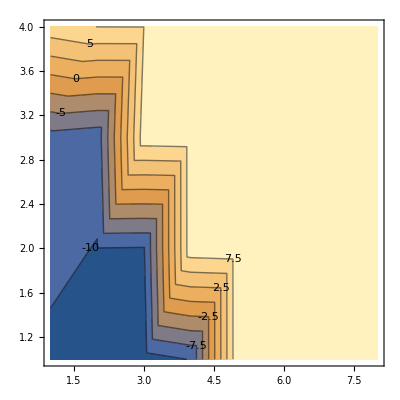

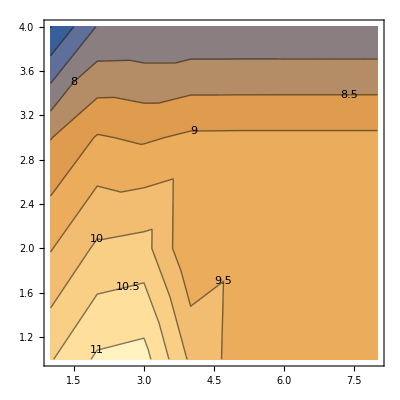

```mathematica
ListContourPlot[Table[Sign[MgOλeDictSI["EnergyLossMesh"]][[i,j]]Abs[Log10[MgOλeDictSI["EnergyLossMesh"]][[i,j]]],{j,MgOλeDictSI["meshdims"]["vχ"]},{i,MgOλeDictSI["meshdims"]["mχ"]}],ContourLabels->True]
ListContourPlot[Table[Abs[Log10[MgOλeDictSI["EnergyLossMesh"]][[i,j]]],{j,MgOλeDictSI["meshdims"]["vχ"]},{i,MgOλeDictSI["meshdims"]["mχ"]}],ContourLabels->True]
```

#### test kinematics

```mathematica
ω== ((ℏ q)/mχ).(mχ v-(ℏ q)/2)
```

ω==(q ℏ)/mχ.(mχ v-(q ℏ)/2)

```mathematica
Solve[ER==q^2/(2 mT) + u q vT,q]
```

{{q→-mT u vT-√mT √(2 ER+mT u^2 vT^2)},{q→-mT u vT+√mT √(2 ER+mT u^2 vT^2)}}

```mathematica
Integrate[f[q] DiracDelta[ω - q v u + (ℏ q^2)/(2 mχ)],q]
```

2 ∫DiracDelta[-2 q u v+2 ω+(q^2 ℏ)/mχ] f[q]ⅆq

```mathematica
Solve[ω - (ℏ q^2)/(2 mχ) + u q v==0,q]
q0 = q/.(%[[2]])
Simplify[D[ω - (ℏ q^2)/(2 mχ) + u q v,q]]
Simplify[%/.q->q0]
```

{{q→-(mχ (-u v+(√(mχ u^2 v^2+2 ω ℏ))/(√mχ)))/ℏ},{q→(mχ u v+√mχ √(mχ u^2 v^2+2 ω ℏ))/ℏ}}

(mχ u v+√mχ √(mχ u^2 v^2+2 ω ℏ))/ℏ

u v-(q ℏ)/mχ

-(√(mχ u^2 v^2+2 ω ℏ))/(√mχ)